# Pose Stabilization of a Bar Tethered to Two Aerial Vehicles

```mathematica
(*title*)
```

# Linearization in manifold

This procedure is explained in companion pdf

```mathematica
Linearization[
VectorField_,(*vector field*)
SetDefiningConstraints_,(*constraints that define state space where vector field is defined*)
EquilibriumPoint_,(*equilibrium point around which linearization is performed*)
ApplySimplifications_(*any simplifications that the user may deem appropriate: e.g., parameter "m" is positive*)
]:=
Module[{
Z=VectorField,
C=SetDefiningConstraints,CCT,Proj,
z=Array[Subscript[z, #]&,Length[EquilibriumPoint]],
DC,A0,A1
},

(*NewVectorField = Z[z] - Transpose[DC[zeq]].Inverse[DC[zeq].Transpose[DC[zeq]]]].(DC[z].Z[z]+λ C[z]);*)

DC=ApplySimplifications[D[C[z],{z}]/.Thread[z-> EquilibriumPoint]];(*derivative of constraints map*)
CCT=ApplySimplifications[Transpose[DC].Inverse[DC.Transpose[DC]].DC];
Proj=IdentityMatrix[Length[EquilibriumPoint]]-CCT;(*projection onto space orthogonal to DC*)

A0=ApplySimplifications[D[Z[z],{z}]/.Thread[z-> EquilibriumPoint]];(*state matrix*)
A1=ApplySimplifications[Proj.A0-λ CCT];(*modified state matrix that is easier to analyze*)
{A0,A1}
]

(*Linearization[
VectorField_,
SetDefiningConstraints_,
EquilibriumPoint_,
ApplySimplifications_
]:=
Module[{
Z=VectorField,
C=SetDefiningConstraints,CCT,Proj,
z=Array[Subscript[z, #]&,Length[EquilibriumPoint]],
DC,A0,A1
},

(*NewVectorField = Z[z] - Transpose[DC[zeq]].Inverse[DC[zeq].Transpose[DC[zeq]]]].(DC[z].Z[z]+λ C[z]);*)

DC=ApplySimplifications[D[C[z],{z}]/.Thread[z-> EquilibriumPoint]];
CCT=Transpose[DC].Inverse[DC.Transpose[DC]].DC;
Proj=IdentityMatrix[Length[EquilibriumPoint]]-CCT;

A0=D[Z[z],{z}]/.Thread[z-> EquilibriumPoint];
A1=ApplySimplifications[Proj.A0-λ CCT];
{A0,A1}
]
*)
```

# Routh’s Criterion

## Controllable canonical form matrix

```mathematica
addrow[a_]:=Join[{UnitVector[Length[a],Length[a]+1-Dimensions[#][[1]]]},#]&
CC[a_]:=Nest[addrow[a],{-a},Length[a]-1]
CC[{a0,a1,a2}]//MatrixForm
CC[{a0,a1,a2,a3}]//MatrixForm
CC[{a0,a1,a2,a3,a4}]//MatrixForm
```

(0 | 1 | 0
0 | 0 | 1
-a0 | -a1 | -a2)

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
-a0 | -a1 | -a2 | -a3)

(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
-a0 | -a1 | -a2 | -a3 | -a4)

## Hurwitz conditions

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"hurwitz_conditions.nb"}]];
```

## Γ3 (all terms need to be positive: in first column of Routh’s table)

```mathematica
ΓΓ3={fd (kp+fp) ,fd kd+fp,fd};
CC[ΓΓ3]//MatrixForm
Step4[CC[ΓΓ3]]//MatrixForm
```

(0 | 1 | 0
0 | 0 | 1
-fd (fp+kp) | -fp-fd kd | -fd)

(1
fd
fd (fd kd-kp)
fd (fp+kp))

## Γ5 (all terms need to be positive: in first column of Routh’s table)

```mathematica
ΓΓ5=-(-{fd fp kp ,fp fd kv,fd(kp+ fp (1+q)) ,fd kv+fp (1+q),fd});
CC[ΓΓ5]//MatrixForm
Step4[CC[ΓΓ5]]//MatrixForm
```

(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
-fd fp kp | -fd fp kv | -fd (kp+fp (1+q)) | -fd kv-fp (1+q) | -fd)

(1
fd
fd (-kp+fd kv)
fd^2 (-kp+fd kv) (kp+fp q)
fd^2 fp^2 (kp-fd kv)^2 q
fd fp kp)

## Γ4 (all terms need to be positive: in first column of Routh’s table)

```mathematica
ΓΓ4=-(-{ fp kp ,fp kv,kp+ fp (1+q) , kv});
CC[ΓΓ4]//MatrixForm
Step4[CC[ΓΓ4]]//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
-fp kp | -fp kv | -kp-fp (1+q) | -kv)

(1
kv
kv (kp+fp q)
fp^2 kv^2 q
fp kp)

## Γ4tilde (all terms need to be positive: in first column of Routh’s table)

```mathematica
ΓΓ4=-(-{ fp (kp+fp q qt) ,fp kv,kp+ fp (1+q) , kv});
CC[ΓΓ4]//MatrixForm
Step4[CC[ΓΓ4]]//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
-fp (kp+fp q qt) | -fp kv | -kp-fp (1+q) | -kv)

(1
kv
kv (kp+fp q)
-fp^2 kv^2 q (-1+qt)
fp (kp+fp q qt))

# Crane system

## check notebook at “crane_system/crane_system”.nb

## Relations with specific physical constants

```mathematica
PhysicalConstants={
gravity->9.81,
m1 ->2.222,(*neo mass*)
m2-> 2.733+0.8,(*popeye mass + robotic arm*)
L1-> 1.45,(*cable length neo*)
L2->1.2 ,(*cable length popeye*)
d1-> -1,
d2-> 1
};
PhysicalConstants=Join[
PhysicalConstants,
{
J-> d1 m1 gravity+d2 m2 gravity+1/12 mbar (Abs[d1]+Abs[d2])^2(*d1*m1*g+d2*m2*g+1/12 mbar L^2*),
m-> m1+m2+mbar
}/.{m1-> 0.587,m2-> 0.608,mbar-> 0.287}/.PhysicalConstants
];
```

# Notation

```mathematica
(*Orthogonal projection matrix to x ∈ S^2*)
OP[x_]:=IdentityMatrix[3]-KroneckerProduct[x, x]
(*Skew symmetric matrix*)
Skew[ω_]:={{0,-ω[[3]],ω[[2]]},{ω[[3]],0,-ω[[1]]},{-ω[[2]],ω[[1]],0}}
```

#### Parametrization of unit vector with psi and theta angle

```mathematica
(*uv1[{0,0}] = e1*)
uv1[{θ1_,θ2_}]={Cos[θ2]Cos[θ1],Cos[θ2]Sin[θ1],-Sin[θ2]};
(*uv3[{0,0}] = e3*)
uv3[{θ1_,θ2_}]={Cos[θ2] Sin[θ1],Sin[θ2],Cos[θ1] Cos[θ2]};

Duv1[{θ1_,θ2_},{ω1_,ω2_}]=Evaluate[D[uv1[{θ1,θ2}],{{θ1,θ2}}]].{ω1,ω2};
Duv3[{θ1_,θ2_},{ω1_,ω2_}]=Evaluate[D[uv3[{θ1,θ2}],{{θ1,θ2}}]].{ω1,ω2};

(*just checking orthogonality*)
(*uv1[{ψ,θ}].Duv1[{ψ,θ},{ωψ,ωθ}]//Simplify*)
(*uv3[{ψ,θ}].Duv3[{ψ,θ},{ωψ,ωθ}]//Simplify*)
```

```mathematica
{{1,0,0},{0,1,0}}.OP[{Cos[ψ],Sin[ψ],0}]//Simplify//MatrixForm
```

(Sin[ψ]^2 | -Cos[ψ] Sin[ψ] | 0
-Cos[ψ] Sin[ψ] | Cos[ψ]^2 | 0)

# Fully-actuated UAVs

## State and input decomposition (these are dummy names)

```mathematica
(*kinematic state*)
p={px,py,pz};
n={nx,ny,nz};
P1={p1x,p1y,p1z};
P2={p2x,p2y,p2z};
zk=Join[p,n,P1,P2];

(*dynamic state*)
v={vx,vy,vz};
ω={ωx,ωy,ωz};
V1={v1x,v1y,v1z};
V2={v2x,v2y,v2z};
zd=Join[v,ω,V1,V2];


(*full state*)
z1=Join[zk,zd];
(*input*)
u1={u1x,u1y,u1z};
u2={u2x,u2y,u2z};
u=Join[u1,u2];
```

## State set (in manuscript Z1SET is called f)

```mathematica
Z1SET[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=
{
(((#.#)/L1^2 - 1)&)[P1-(p+d1 n)],
(((#.#)/L2^2- 1)&)[P2-(p+d2 n)],
((#1.#2)/L1^2 &)[P1-(p+d1 n),V1-(v+d1 Skew[ω].n)],
((#1.#2)/L2^2 &)[P2-(p+d2 n),V2-(v+d2 Skew[ω].n)],
n.n-1,
n.ω
};
```

## Tangent set

```mathematica
δp={δpx,δpy,δpz};δn={δnx,δny,δnz};δP1={δp1x,δp1y,δp1z};δP2={δp2x,δp2y,δp2z};
δv={δvx,δvy,δvz};δω={δωx,δωy,δωz};δV1={δv1x,δv1y,δv1z};δV2={δv2x,δv2y,δv2z};
δz1=Join[δp,δn,δP1,δP2,δv,δω,δV1,δV2];

TangentZ1SET[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},
{δpx_,δpy_,δpz_,δnx_,δny_,δnz_,δp1x_,δp1y_,δp1z_,δp2x_,δp2y_,δp2z_,δvx_,δvy_,δvz_,δωx_,δωy_,δωz_,δv1x_,δv1y_,δv1z_,δv2x_,δv2y_,δv2z_}
]={
(#1.#2 &)[P1-(p+d1 n),δP1-(δp+d1 δn)],
(#1.#2&)[P2-(p+d2 n),δP2-(δp+d2 δn)],
(#3.#2+#1.#4 &)[P1-(p+d1 n),V1-(v+d1 Skew[ω].n),δP1-(δp+d1 δn),δV1-(δv+d1 Skew[δω].n+d1 Skew[ω].δn)],
(#3.#2+#1.#4 &)[P2-(p+d2 n),V2-(v+d2 Skew[ω].n),δP2-(δp+d2 δn),δV2-(δv+d2 Skew[δω].n+d2 Skew[ω].δn)],
n.δn,
δn.ω+n.δω
};
```

## Function that generates random element in state set

```mathematica
z1l[l_]:=Join[
p,
uv1[{θ1,θ2}],
p+d1 uv1[{θ1,θ2}]+L1 uv3[{α11,α12}],
p+d2 uv1[{θ1,θ2}]+L2 uv3[{α21,α22}],
v,
Skew[uv1[{θ1,θ2}]].Duv1[{θ1,θ2},{θ1d,θ2d}],
v+d1 Duv1[{θ1,θ2},{θ1d,θ2d}]+L1 Duv3[{α11,α12},{α11d,α12d}],
v+d2 Duv1[{θ1,θ2},{θ1d,θ2d}]+L2 Duv3[{α21,α22},{α21d,α22d}]
]/.Thread[Join[p,{θ1,θ2},{α11,α12},{α21,α22},v,{θ1d,θ2d},{α11d,α12d},{α21d,α22d}]-> l]

z1lR[]:=z1l[ RandomReal[{-0.2,0.2},18]]
(*z1lR[]*)
Chop[Z1SET[z1l[Array[Subscript[y, #]&,18]]]]//Simplify
```

{0,0,0,0,0,0}

## Vector field (Z1 is called Z in article)

```mathematica
(*cables unit vectors*)
nC1[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=(P1-(p+d1 n))/L1;
nC2[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=(P2-(p+d2 n))/L2;

(*tensions in cables*)
MT[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=(DiagonalMatrix[{m/m1,m/m2}]+{{1,γ},{γ,1}}+(m d1 d2)/J{{d1/d2 δ1.δ1,δ1.δ2},{δ1.δ2,d2/d1 δ2.δ2}})/.{γ-> nC1[z1].nC2[z1],δ1-> Skew[n].nC1[z1],δ2-> Skew[n].nC2[z1]};

BB[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]=
{
(nC1[z1].u1 m/m1+m/L1(#.#&)[V1-(v+d1 Skew[ω].n)]+ m d1 nC1[z1].n (#.#&)[ω]),
(nC2[z1].u2 m/m2+m/L2(#.#&)[V2-(v+d2 Skew[ω].n)]+ m d2 nC2[z1].n (#.#&)[ω])
};
Te[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]=Inverse[MT[zk]].BB[z1,u];


(*linear and angular accelerations*)
a[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]=1/m(T1 nC1[z1]+T2 nC2[z1]- m gravity {0,0,1})/.Thread[{T1,T2}-> Te[z1,u]];
τB[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]=1/J(Skew[d1 n].nC1[z1] T1 + Skew[d2 n].nC2[z1]T2)/.Thread[{T1,T2}-> Te[z1,u]];
A1[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]= 1/m1(u1-T1 nC1[z1]- m1 gravity {0,0,1})/.Thread[{T1,T2}-> Te[z1,u]];
A2[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]= 1/m2(u2-T2 nC2[z1]- m2 gravity{0,0,1})/.Thread[{T1,T2}-> Te[z1,u]];

Zk[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Join[
v,
Skew[ω].n,
V1,
V2
];

Zd[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]=Join[
a[z1,u],
τB[z1,u],
A1[z1,u],
A2[z1,u]
];

Z1 [{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]=Join[
Zk[z1],
Zd[z1,u]
];
```

## Check that vector field is within tangent set

```mathematica
Chop[
Evaluate[D[Z1SET[z1],{z1}]].Z1[z1,u]/.Thread[z1-> z1lR[]]/.
Thread[{gravity,m,J,L1,L2,m1,m2,d1,d2}-> RandomReal[{1,10},9]]/.
Thread[u-> RandomReal[{-10,10},6]]
]
```

{0,0,0,0,0,0}

## Equilibrium input

```mathematica
u1eq[{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=T {nxd,nyd,nzd}+{0,0,1}(m1 gravity +(d2 gravity m)/(d2-d1));
u2eq[{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=-T {nxd,nyd,nzd}+{0,0,1}(m2 gravity +(d1 gravity m)/(d1-d2));
ueq[{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=Join[u1eq[{pxd,pyd,pzd,T,nxd,nyd,nzd}],u2eq[{pxd,pyd,pzd,T,nxd,nyd,nzd}]];
```

## Equilibrium state

```mathematica
z1eq[{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=Join[
#p,
#n,
#p+d1#n+L1(#/(√(#.#))&[(d2 m gravity)/(d2-d1){0,0,1}+T#n]),
#p+d2#n+L2(#/(√(#.#))&[(d1 m gravity)/(d1-d2){0,0,1}-T#n]),
{0,0,0},
{0,0,0},
{0,0,0},
{0,0,0}
]&[<|"n"-> {nxd,nyd,nzd},"p"-> {pxd,pyd,pzd}|>];
```

```mathematica
(*test*)
z1eq[{0,0,0,0,1,0,0}]/.{d1-> 1,d2->- 1,L1-> 1,L2-> 1,m-> 1,gravity-> 10}
```

{0,0,0,1,0,0,1,0,1,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0}

## Check vector field vanishes at equilibrium

```mathematica
(*Z1[z1eq[#],ueq[#]]&[{0,0,0,T,Cos[α],0,Sin[α]}]//Simplify*)
Z1[z1eq[#],ueq[#]]&[{pxd,pyd,pzd,T,Cos[α],0,Sin[α]}]//Simplify
(*you may also check the one below*)
(*Z1[z1eq[#],ueq[#]]&[{pxd,pyd,pzd,T,Cos[α]Cos[ψ],Cos[α]Sin[ψ],-Sin[α]}]//Simplify*)
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Matrix N

### Accelerations are linear in tensions, i.e., V̇= ...+N (T_1,T_2)

```mathematica
NN[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=Transpose[
{
Join[1/m nC1[z1],(Skew[d1 n].nC1[z1])/J,-1/m1 nC1[z1],{0,0,0}],
Join[1/m nC2[z1],(Skew[d2 n].nC2[z1])/J,{0,0,0},-1/m2 nC2[z1]]
}
];
```

## Vector field is input affine

```mathematica
BlockDiagonalMatrix[b:{__?MatrixQ}]:=Module[{r,c,n=Length[b],i,j},{r,c}=Transpose[Dimensions/@b];
ArrayFlatten[Table[If[i==j,b[[i]],ConstantArray[0,{r[[i]],c[[j]]}]],{i,n},{j,n}]]]
```

### dynamics (v̇=A+Bu) B matrix below

```mathematica
BU[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=Transpose[KroneckerProduct[{{0,0,1/m1,0},{0,0,0,1/m2}},IdentityMatrix[3]]]+
NN[zk].Inverse[MT[zk]].{Join[m/m1 nC1[z1],{0,0,0}],Join[{0,0,0},m/m2 nC2[z1]]};
```

### Confirm vector field is input affine

```mathematica
error[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]= Zd[z1,u]-(Zd[z1,{0,0,0,0,0,0}]+BU[zk].u);
Chop[error[z1lR[],RandomReal[{-1,1},6]]/.
Thread[{gravity,m,J,L1,L2,m1,m2,d1,d2}-> RandomReal[{1,10},9]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0}

## Checking momentum independence from Tensions

### linear and angular momentum w.r.t. bar’s center of mass

```mathematica
PP[{vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=m v + m1 V1 + m2 V2;
HH[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_},{vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=J ω + Skew[d1 n + l1 nC1[z1]].(m1 V1) + Skew[d2 n + l2 nC2[z1]].(m2 V2);
```

```mathematica
D[PP[zd],{zd}].NN[zk]//Simplify
D[HH[zk,zd],{zd}].NN[zk]//Simplify
```

{{0,0},{0,0},{0,0}}

{{0,0},{0,0},{0,0}}

### angular momentum written w.r.t. an arbitrary point

```mathematica
PP[{vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=m v + m1 V1 + m2 V2;
HH[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_},{vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=J ω + Skew[{o1,o2,o3}+d1 n + l1 nC1[z1]].(m1 V1) + Skew[{o1,o2,o3}+d2 n + l2 nC2[z1]].(m2 V2)+ Skew[{o1,o2,o3}].(m v);
```

```mathematica
D[PP[zd],{zd}].NN[zk]//Simplify
D[HH[zk,zd],{zd}].NN[zk]//Simplify
```

{{0,0},{0,0},{0,0}}

{{0,0},{0,0},{0,0}}

## invariance to translations and rotations around vertical

```mathematica
TRo[z1_,R_,o_]:=Join[
R.(z1[[1;;3]]-o),
R.z1[[4;;6]],
R.(z1[[7;;9]]-o),
R.(z1[[10;;12]]-o),
R.z1[[13;;15]],
R.z1[[16;;18]],
R.z1[[19;;21]],
R.z1[[22;;24]]
]
```

#### rotational around vertical

```mathematica
Rvertical=(Transpose[{(OP[#2].#1)/(√(1-(#1.#2)^2)),(Skew[#2].#1)/(√(1-(#1.#2)^2)),#2}])&[{Cos[θ]Cos[ψ],Cos[θ]Sin[ψ],-Sin[θ]},{0,0,1}]
```

{{(Cos[θ] Cos[ψ])/(√(1-Sin[θ]^2)),-(Cos[θ] Sin[ψ])/(√(1-Sin[θ]^2)),0},{(Cos[θ] Sin[ψ])/(√(1-Sin[θ]^2)),(Cos[θ] Cos[ψ])/(√(1-Sin[θ]^2)),0},{0,0,1}}

#### invariance of open-loop vector field

```mathematica
BlockDiagonalMatrix[b:{__?MatrixQ}]:=Module[{r,c,n=Length[b],i,j},{r,c}=Transpose[Dimensions/@b];
ArrayFlatten[Table[If[i==j,b[[i]],ConstantArray[0,{r[[i]],c[[j]]}]],{i,n},{j,n}]]]
(* too complicated for mathematica, because tensions involve the inversion of a matrix*)
(*(Z1[TRo[z1,#,{ox,oy,oz}],Join[#.u1,#.u2]]-BlockDiagonalMatrix[{#,#,#,#,#,#,#,#}].Z1[z1,u]&[Rvertical])//Simplify*)

(* tensions are invariant to rotations and translations*)
MT[TRo[z1,#,{ox,oy,oz}][[1;;12]]]-MT[z1[[1;;12]]]&[Rvertical]//Simplify
BB[TRo[z1,#,{ox,oy,oz}],Join[#.u1,#.u2]]-BB[z1,u]&[Rvertical]//Simplify

(*proving that Z is invariant to rotations and translations is easy after showing that tensions are invariant to rotations and translations*)
```

{{0,0},{0,0}}

{0,0}

## Control law for each uav

rotation

```mathematica
Rnγ[{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=(Transpose[{(OP[#2].#1)/(√(1-(#1.#2)^2)),(Skew[#2].#1)/(√(1-(#1.#2)^2)),#2}])&[{nxd,nyd,nzd},{0,0,1}];
```

relations that involve to Rnγ

```mathematica
RnγAUX=Rnγ[{px,py,pz,T,Cos[θ]Cos[ψ],Cos[θ]Sin[ψ],-Sin[θ]}];
(Transpose[RnγAUX].{0,0,1})-{0,0,1}//Simplify
(Transpose[RnγAUX].{Cos[θ]Cos[ψ],Cos[θ]Sin[ψ],-Sin[θ]})-{√(Cos[θ]^2),0,-Sin[θ]}//Simplify

Transpose[Rnγ[#]].u1eq [#]-u1eq [{0,0,0,T,√(Cos[θ]^2),0,-Sin[θ]}]&[{px,py,pz,T,Cos[θ]Cos[ψ],Cos[θ]Sin[ψ],-Sin[θ]}]//Simplify
Transpose[Rnγ[#]].u2eq [#]-u2eq [{0,0,0,T,√(Cos[θ]^2),0,-Sin[θ]}]&[{px,py,pz,T,Cos[θ]Cos[ψ],Cos[θ]Sin[ψ],-Sin[θ]}]//Simplify
```

{0,0,0}

{0,0,0}

{0,0,0}

«1 more identical outputs»

proportional and derivative gains

```mathematica
Kp1=DiagonalMatrix[{kpx1,kpy1,kpz1}];
Kd1=DiagonalMatrix[{kvx1,kvy1,kvz1}];
Kp2=DiagonalMatrix[{kpx2,kpy2,kpz2}];
Kd2=DiagonalMatrix[{kvx2,kvy2,kvz2}];
```

pd control law for UAV 1 and 2: unsaturated version

```mathematica
u1PD[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=-m1  Rnγ[#].(
Kp1.Transpose[Rnγ[#]].({p1x,p1y,p1z}-z1eq[#][[7;;9]])+
Kd1.Transpose[Rnγ[#]].{v1x,v1y,v1z}
)+
m1 d1 L1/(L1+L2){0,0,1}.(kpψ1 Skew[{nxd,nyd,nzd}].{nx,ny,nz}+kvψ1{ωx,ωy,ωz} )Rnγ[#].{0,1,0}&[{pxd,pyd,pzd,T,nxd,nyd,nzd}];
u2PD[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=-m2  Rnγ[#].(
Kp2.Transpose[Rnγ[#]].({p2x,p2y,p2z}-z1eq[#][[10;;12]])+
Kd2.Transpose[Rnγ[#]].{v2x,v2y,v2z}
)+m2 d2 L2/(L1+L2){0,0,1}.(kpψ2 Skew[{nxd,nyd,nzd}].{nx,ny,nz}+kvψ2{ωx,ωy,ωz} )Rnγ[#].{0,1,0}&[{pxd,pyd,pzd,T,nxd,nyd,nzd}];
```

#### include feedforward term

```mathematica
(*pd control law for for each direction*)
u1clComplete[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=
(ueq[#][[1;;3]])+u1PD[z1,#]&[{pxd,pyd,pzd,T,nxd,nyd,nzd}];

u2clComplete[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=
(ueq[#][[4;;6]])+u2PD[z1,#]&[{pxd,pyd,pzd,T,nxd,nyd,nzd}];
```

combine control laws of UAVs

```mathematica
(*complete control law*)
ucl[z_,γ_]:=Join[u1clComplete[z,γ],u2clComplete[z,γ]]
```

Verify that we only really need to consider γ=(0,0,0,T,√(Cos[θ]^2),0,Sin[θ])

```mathematica
(*u1clComplete[#1,#2]-Rnγ[#2].u1clComplete[TRo[#1,Transpose[Rnγ[#2]],#2[[1;;3]]],{0,0,0,T,√(Cos[θ]^2),0,Sin[θ]}]&[z1l[Array[Subscript[x, #]&,18]],{0,0,0,T,Cos[θ],0,Sin[θ]}]//Simplify*)

(*only verified for UAV 1, but can also be verified for UAV 2*)
u1clComplete[#1,#2]-Rnγ[#2].u1clComplete[TRo[#1,Transpose[Rnγ[#2]],#2[[1;;3]]],{0,0,0,T,√(Cos[θ]^2),0,Sin[θ]}]&[z1l[Array[Subscript[x, #]&,18]],{px,py,pz,T,Cos[θ]Cos[ψ],Cos[θ]Sin[ψ],Sin[θ]}]//Simplify
```

{0,0,0}

pd control law for UAV 1 and 2: Saturated

### saturation function

```mathematica
σ3D[{x_,y_,z_}]:={σ[x],σ[y],σ[z]}
```

### saturated PD

```mathematica
u1PDSaturated[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=-m1  Rnγ[#].(
Kp1.σ3D[Transpose[Rnγ[#]].({p1x,p1y,p1z}-z1eq[#][[7;;9]])]+
Kd1.σ3D[Transpose[Rnγ[#]].{v1x,v1y,v1z}]
)+
m1 d1 L1/(L1+L2)(kpψ1 {0,0,1}.Skew[{nxd,nyd,nzd}].{nx,ny,nz}+kvψ1 σ[ωz] )Rnγ[#].{0,1,0}&[{pxd,pyd,pzd,T,nxd,nyd,nzd}];
u2PDSaturated[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=-m2  Rnγ[#].(
Kp2.σ3D[Transpose[Rnγ[#]].({p2x,p2y,p2z}-z1eq[#][[10;;12]])]+
Kd2.σ3D[Transpose[Rnγ[#]].{v2x,v2y,v2z}]
)+m2 d2 L2/(L1+L2)(kpψ2 {0,0,1}.Skew[{nxd,nyd,nzd}].{nx,ny,nz}+kvψ2 σ[ωz] )Rnγ[#].{0,1,0}&[{pxd,pyd,pzd,T,nxd,nyd,nzd}];
```

#### include feedforward term

```mathematica
(*pd control law for for each direction*)
u1clCompleteSaturated[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=
(ueq[#][[1;;3]])+u1PDSaturated[z1,#]&[{pxd,pyd,pzd,T,nxd,nyd,nzd}];

u2clCompleteSaturated[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=
(ueq[#][[4;;6]])+u2PDSaturated[z1,#]&[{pxd,pyd,pzd,T,nxd,nyd,nzd}];

(*complete control law*)
uclSaturated[z_,γ_]:=Join[u1clCompleteSaturated[z,γ],u2clCompleteSaturated[z,γ]]
```

Verify that saturation does not play a role when we linearize (so, we can ignore saturations)
σ[0]=0
σ’[0]=1

#### input with and without saturations is the same at the equilibrium

```mathematica
Simplify[uclSaturated[z1,#]-ucl[z1,#]/.Thread[z1-> z1eq[#]]&[{pxd,pyd,pzd,T,nxd,nyd,nzd}],σ[0]==0]
```

{0,0,0,0,0,0}

#### note that equilibrium point is the same for the unsaturated and the saturated control laws (that is not the case when there is an integral term)

```mathematica
ans1=Simplify[D[u1clCompleteSaturated[z1,#],{z1}]/.Thread[z1-> z1eq[#]]&[{0,0,0,T,√(Cos[θ]^2),0,Sin[θ]}],σ'[0]==  1];
ans2=D[u1clComplete[z1,#],{z1}]/.Thread[z1-> z1eq[#]]&[{0,0,0,T,√(Cos[θ]^2),0,Sin[θ]}]//Simplify;
ans1-ans2//Simplify
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
ans1=Simplify[D[u2clCompleteSaturated[z1,#],{z1}]/.Thread[z1-> z1eq[#]]&[{0,0,0,T,√(Cos[θ]^2),0,Sin[θ]}],σ'[0]==  1];
ans2=D[u2clComplete[z1,#],{z1}]/.Thread[z1-> z1eq[#]]&[{0,0,0,T,√(Cos[θ]^2),0,Sin[θ]}]//Simplify;
ans1-ans2//Simplify
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

## check that control law matches equilibrium input at desired equilibrium point

```mathematica
(ucl[z1eq[#],#]-ueq[#])&[{pxd,pyd,pzd,T,Cos[α],0,Sin[α]}]//Simplify
```

{0,0,0,0,0,0}

## check that there are other equilibria points

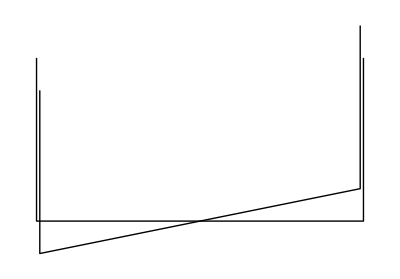

```mathematica
ConfigurationGraphics2D[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]:=
Graphics[
Line[{{p1x,p1z},{px,pz}+d1 {nx,nz},{px,pz}+d2 {nx,nz},{p2x,p2z}}]
]
(*test*)
Show[
ConfigurationGraphics2D[z1eq[{0,0,0,0,1,0,0}]]/.{d1-> 1,d2-> -1,L1-> 1,L2-> 1,m-> 1,gravity-> 10},
ConfigurationGraphics2D[z1eq[{0,0,0,0,Cos[0.2],0,Sin[0.2]}]]/.{d1-> 1,d2-> -1,L1-> 1,L2-> 1,m-> 1,gravity-> 10}
]
```

```mathematica
(*Module[{
frac=1/3,
γOrignal,
γOther,
configurationOriginal,configurationOrther
},
γOrignal={0,0,0,0,1,0,0};
γOther={0,0,(1-1/(√(1+4 frac^2))) L ,-frac gravity m,-1,0,0};
Print["Different equilibrium"];
Print[
Simplify[
ucl[z1eq[γOther],γOrignal]-ueq[γOther]/.{d1-> d,d2-> -d,L1-> L,L2-> L,kpx1-> kp,kpx2-> kp,m1->M,m2->M}/.{kp->(frac √(1+4 frac^2) gravity m)/(2 (d √(1+4 frac^2)-frac L) M)},
gravity>0&& m>0
]
];
Print["UAVs at same height for different equilibria"];
Print[
Simplify[
(z1eq[γOrignal]-z1eq[γOther])[[{9,12}]]/.{d1-> d,d2-> -d,L1-> L,L2-> L ,kpx1-> kp,kpx2-> kp,m1->M,m2->M},
gravity>0&& m>0
]
];
Print["x-gain proportional gain that does the job: " ,(frac √(1+4 frac^2) gravity m)/(2 (d √(1+4 frac^2)-frac L) M)/.{d-> 1,L-> 1,m-> 1,gravity-> 10,M-> 2}//N];
configurationOriginal=ConfigurationGraphics2D[z1eq[γOrignal]]/.{d1-> d,d2-> -d,L1-> L,L2-> L}/.{d-> 1,L-> 1,m-> 1,gravity-> 10};
configurationOrther=ConfigurationGraphics2D[z1eq[γOther]]/.{d1-> d,d2-> -d,L1-> L,L2-> L}/.{d-> 1,L-> 1,m-> 1,gravity-> 10};
Show[configurationOriginal,configurationOrther]
]*)
```

## Closed loop vector field

```mathematica
Z1cl[z_,γ_]:=Z1[z,ucl[z,γ]]
```

## Check it vanishes at equilibrium

```mathematica
Z1cl[z1eq[#],#]&[{0,0,0,0,1,0,0}]//FullSimplify
(*you may also check the one below: but it takes longer*)
(*Z1cl[z1eq[#],#]&[{pxd,pyd,pzd,T,Cos[α],0,Sin[α]}]//FullSimplify*)
(*you may also check the one below: but it takes longer*)
(*Z1cl[z1eq[#],#]&[{pxd,pyd,pzd,T,Cos[α]Cos[ψ],Cos[α]Sin[ψ],-Sin[α]}]//Simplify*)
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

# Symmetric T=0 and θ=0

#### equilibrium parametrization

```mathematica
Subscript[γ, eq,1]={0,0,0,0,1,0,0};
```

## Simplification

```mathematica
SimplificationsParameters={d1-> d,d2-> -d,m1-> M, m2-> M,L1-> L,L2-> L};
SimplificationsGains={kpx1-> kpx,kvx1-> kvx,kpy1-> kpy,kvy1-> kvy,kpz1-> kpz,kvz1-> kvz,kpx2-> kpx,kvx2-> kvx,kpy2-> kpy,kvy2-> kvy,kpz2-> kpz,kvz2-> kvz,kpψ1-> 0,kvψ1-> 0,kpψ2-> 0,kvψ2-> 0};
Simplifications=Join[SimplificationsParameters,SimplificationsGains];

ApplySimplificationsParameters=Simplify[#/.SimplificationsParameters,gravity>0 &&m>0&&d1<0&&d2> 0]&;
ApplySimplificationsGains=Simplify[#/.SimplificationsGains]&;
ApplySimplifications=Simplify[#/.Simplifications,gravity>0 &&m>0&&d1<0&&d2> 0]&;
```

## Stability vector field term (only for analysis)

```mathematica
DZ1SET[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Evaluate[D[Z1SET[z1],{z1}]];
```

## determinant of matrix being inverted is positive

```mathematica
(*Simplify[Inverse[#.Transpose[#]]&[DZ1SET[z1eq[{0,0,0,0,1,0,0}]]],gravity>0& m>0&& d1>0&& d2<0]//MatrixForm
Simplify[Inverse[#.Transpose[#]]&[DZ1SET[z1eq[{0,0,0,0,Cos[α],0,Sin[α]}]]],gravity>0& m>0&& d1>0&& d2<0]//MatrixForm
Simplify[Inverse[#.Transpose[#]]&[DZ1SET[z1eq[{0,0,0,α gravity m,1,0,0}]]],gravity>0& m>0&& d1>0&& d2<0]//MatrixForm*)
```

```mathematica
Simplify[Det[#.Transpose[#]]&[DZ1SET[z1eq[Subscript[γ, eq,1]]]]- (64 (3+{d1,d2}.{{2,-1},{-1,2}}.{d1,d2})^2)/(L1^4 L2^4)]
```

0

## Linearization matrix

```mathematica
{Subscript[A, 0],Subscript[A, 1]}=Linearization[
Z1cl[#,Subscript[γ, eq,1]]&,
Z1SET[#]&,
z1eq[Subscript[γ, eq,1]],
ApplySimplificationsParameters
];
(*Subscript[A, 0]//MatrixForm*)
(*Subscript[A, 1]//MatrixForm*)
```

## Similarity matrix

```mathematica
(*unit vector of dimension of state*)
e[i_]:=UnitVector[Dimensions[z1][[1]],i];
```

```mathematica
chainOfIntegrators[e_,n_,A_]:=NestList[Evaluate[ApplySimplificationsParameters[#.A]]&,e,n-1]
chainOfIntegrators[e[1],4,Subscript[A, 1]]//MatrixForm
chainOfIntegrators[e[1],4,Subscript[A, 1]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-gravity/L | 0 | 0 | 0 | 0 | 0 | gravity/(2 L) | 0 | 0 | gravity/(2 L) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -gravity/L | 0 | 0 | 0 | 0 | 0 | gravity/(2 L) | 0 | 0 | gravity/(2 L) | 0 | 0)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-gravity/L | 0 | 0 | 0 | 0 | 0 | gravity/(2 L) | 0 | 0 | gravity/(2 L) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -gravity/L | 0 | 0 | 0 | 0 | 0 | gravity/(2 L) | 0 | 0 | gravity/(2 L) | 0 | 0)

```mathematica
PA[A_]:=
 ApplySimplificationsParameters[
Join[
chainOfIntegrators[e[3],2,A],
chainOfIntegrators[e[6],2,A],
chainOfIntegrators[e[7]-e[10],2,A],
chainOfIntegrators[e[1],4,A],
chainOfIntegrators[e[2],4,A],
chainOfIntegrators[e[5],4,A]
]
];

PPA[A_]:=
 ApplySimplificationsParameters[
Join[
PA[A],
DZ1SET[z1eq[Subscript[γ, eq,1]]]
]
];
Subscript[P, 0]=PPA[Subscript[A, 0]];
Subscript[P, 1]=PPA[Subscript[A, 1]];

(*Dimensions[Subscript[P, 0]]*)
(*MatrixRank[Subscript[P, 0]]*)
(*Subscript[P, 0]//MatrixForm*)
(*Subscript[P, 1]//MatrixForm*)
```

## Determinant of similarity matrix

```mathematica
Det[Subscript[P, 0]]-(-(2 d^2 gravity^6 m^2)/(J^2 L^10))//Simplify
Det[Subscript[P, 1]]-(-(2 d^2 gravity^6 m^2)/(J^2 L^10))//Simplify
```

0

0

## State matrix after similarity transformation (check block triangular structure)

```mathematica
(*lin[A_,P_,C_]:=P.(#I-Transpose[C].Inverse[C.Transpose[C]].C).A.(#I-#PN.Inverse[C.#PN].C).Transpose[P].Inverse[P.Transpose[P]]&[<|"I"->IdentityMatrix[Length[A]],"PN"->Transpose[NullSpace[P]]|>]*)
(*Subscript[Asimilar, 2] =ApplySimplificationsGains[lin[Subscript[A, 0],PA[Subscript[A, 0]],DZ1SET[z1eq[Subscript[γ, eq,1]]]]];*)
(*Subscript[Asimilar, 2]//MatrixForm*)
```

```mathematica
(*Subscript[Asimilar, 0] =ApplySimplificationsGains[Subscript[P, 0].Subscript[A, 0].Inverse[Subscript[P, 0]]];*)
(*Subscript[Asimilar, 0]//MatrixForm*)
Subscript[Asimilar, 1] =ApplySimplificationsGains[Subscript[P, 1].Subscript[A, 1].Inverse[Subscript[P, 1]]];
Subscript[Asimilar, 1]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 kpz M)/(m+2 M) | -(2 kvz M)/(m+2 M) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (gravity (-m^2+M^2)-L M (3 kpz M+λ (-2 kvz M+m λ+2 M λ)))/(6 M (m+2 M)) | (gravity (-m^2+M^2)-L M (3 kpz M+λ (-2 kvz M+m λ+2 M λ)))/(6 M (m+2 M)) | -(kvz L M)/(3 m+6 M) | -(kvz L M)/(3 m+6 M) | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(2 d^2 kpz M)/(J+2 d^2 M) | -(2 d^2 kvz M)/(J+2 d^2 M) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(d (gravity (J-M) (m+M)+L M (kpz (M+2 d^2 M)+λ (J λ+2 d^2 M (-kvz+λ)))))/(2 (1+2 d^2) M (J+2 d^2 M)) | (d (gravity (J-M) (m+M)+L M (kpz (M+2 d^2 M)+λ (J λ+2 d^2 M (-kvz+λ)))))/(2 (1+2 d^2) M (J+2 d^2 M)) | -(d kvz L M)/((1+2 d^2) (J+2 d^2 M)) | (d kvz L M)/((1+2 d^2) (J+2 d^2 M)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -kpx-(gravity m)/(2 L M) | -kvx | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (d gravity m)/(2 L M) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(gravity kpx)/L | -(gravity kvx)/L | -(gravity m+2 gravity M+2 kpx L M)/(2 L M) | -kvx | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(gravity kpy)/L | -(gravity kvy)/L | -(gravity m+2 gravity M+2 kpy L M)/(2 L M) | -kvy | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(d^2 gravity kpy m)/(J L) | -(d^2 gravity kvy m)/(J L) | -(2 J kpy L M+gravity m (J+2 d^2 M))/(2 J L M) | -kvy | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ)

## State matrix after similarity transformation (check block triangular structure)

```mathematica
Subscript[Asimilar, 1] =ApplySimplificationsGains[Subscript[P, 1].Subscript[A, 1].Inverse[Subscript[P, 1]]];
Subscript[Asimilar, 1]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 kpz M)/(m+2 M) | -(2 kvz M)/(m+2 M) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (gravity (-m^2+M^2)-L M (3 kpz M+λ (-2 kvz M+m λ+2 M λ)))/(6 M (m+2 M)) | (gravity (-m^2+M^2)-L M (3 kpz M+λ (-2 kvz M+m λ+2 M λ)))/(6 M (m+2 M)) | -(kvz L M)/(3 m+6 M) | -(kvz L M)/(3 m+6 M) | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(2 d^2 kpz M)/(J+2 d^2 M) | -(2 d^2 kvz M)/(J+2 d^2 M) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(d (gravity (J-M) (m+M)+L M (kpz (M+2 d^2 M)+λ (J λ+2 d^2 M (-kvz+λ)))))/(2 (1+2 d^2) M (J+2 d^2 M)) | (d (gravity (J-M) (m+M)+L M (kpz (M+2 d^2 M)+λ (J λ+2 d^2 M (-kvz+λ)))))/(2 (1+2 d^2) M (J+2 d^2 M)) | -(d kvz L M)/((1+2 d^2) (J+2 d^2 M)) | (d kvz L M)/((1+2 d^2) (J+2 d^2 M)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -kpx-(gravity m)/(2 L M) | -kvx | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (d gravity m)/(2 L M) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(gravity kpx)/L | -(gravity kvx)/L | -(gravity m+2 gravity M+2 kpx L M)/(2 L M) | -kvx | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(gravity kpy)/L | -(gravity kvy)/L | -(gravity m+2 gravity M+2 kpy L M)/(2 L M) | -kvy | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(d^2 gravity kpy m)/(J L) | -(d^2 gravity kvy m)/(J L) | -(2 J kpy L M+gravity m (J+2 d^2 M))/(2 J L M) | -kvy | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ)

## Vertical linear and angular motion

```mathematica
Subscript[Asimilar, 1][[1;;4,1;;4]]//MatrixForm
```

(0 | 1 | 0 | 0
-(2 kpz M)/(m+2 M) | -(2 kvz M)/(m+2 M) | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -(2 d^2 kpz M)/(J+2 d^2 M) | -(2 d^2 kvz M)/(J+2 d^2 M))

### vertical linear motion

```mathematica
AofInterest=Subscript[Asimilar, 1][[1;;4,1;;4]][[1;;2,1;;2]];
AofInterest//MatrixForm
```

(0 | 1
-(2 kpz M)/(m+2 M) | -(2 kvz M)/(m+2 M))

```mathematica
Γ2[{fp_,δkp_},{kp_,kd_}]=-{fp (kp+δkp) ,fp kd};
Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[Γ2[{fpz,δkpz},{kpz,kvz}]],
{fpz,δkpz}
]
]
```

{{fpz→(2 M)/(m+2 M),δkpz→0}}

### vertical angular motion

```mathematica
AofInterest=Subscript[Asimilar, 1][[1;;4,1;;4]][[3;;4,3;;4]];
AofInterest//MatrixForm
```

(0 | 1
-(2 d^2 kpz M)/(J+2 d^2 M) | -(2 d^2 kvz M)/(J+2 d^2 M))

```mathematica
Γ2[{fp_,δkp_},{kp_,kd_}]=-{fp (kp+δkp) ,fp kd};
Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[Γ2[{fpz,δkpz},{kpz,kvz}]],
{fpz,δkpz}
]
]
```

{{fpz→(2 d^2 M)/(J+2 d^2 M),δkpz→0}}

## Longitudinal motion

### linear motion

```mathematica
AofInterest=Subscript[Asimilar, 1][[7;;10,7;;10]];
AofInterest//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
-(gravity kpx)/L | -(gravity kvx)/L | -(gravity m+2 gravity M+2 kpx L M)/(2 L M) | -kvx)

```mathematica
Γ4[{fp_,δkp_},{kp_,kd_}]=-{fp kp,fp kd,kp+δkp ,kd};
Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[Γ4[{fpx,δkpx},{kpx,kvx}]],
{fpx,δkpx}
]
]
```

{{fpx→gravity/L,δkpx→(gravity (m+2 M))/(2 L M)}}

### angular motion

```mathematica
AofInterest=Subscript[Asimilar, 1][[5;;6,5;;6]];
AofInterest//MatrixForm
```

(0 | 1
-kpx-(gravity m)/(2 L M) | -kvx)

```mathematica
(*Γ2[{fp_,δkp_},{kp_,kd_}]=-{fp (kp+δkp) ,fp kd};*)
Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[Γ2[{fpx,δkpx},{kpx,kvx}]],
{fpx,δkpx}
]
]
```

{{fpx→1,δkpx→(gravity m)/(2 L M)}}

## Lateral motion

### linear motion

```mathematica
AofInterest=Subscript[Asimilar, 1][[11;;14,11;;14]];
AofInterest//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
-(gravity kpy)/L | -(gravity kvy)/L | -(gravity m+2 gravity M+2 kpy L M)/(2 L M) | -kvy)

```mathematica
Γ4[{fp_,δkp_},{kp_,kd_}]=-{fp kp,fp kd,kp+δkp ,kd};
Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[Γ4[{fpy,δkpy},{kpy,kvy}]],
{fpy,δkpy}
]
]
```

{{fpy→gravity/L,δkpy→(gravity (m+2 M))/(2 L M)}}

### angular motion

```mathematica
AofInterest=Subscript[Asimilar, 1][[15;;18,15;;18]];
AofInterest//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
-(d^2 gravity kpy m)/(J L) | -(d^2 gravity kvy m)/(J L) | -(2 J kpy L M+gravity m (J+2 d^2 M))/(2 J L M) | -kvy)

```mathematica
(*Γ4[{fp_,δkp_},{kp_,kd_}]=-{fp kp,fp kd,kp+δkp ,kd};*)
Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[Γ4[{fpy,δkpy},{kpy,kvy}]],
{fpy,δkpy}
]
]
```

{{fpy→(d^2 gravity m)/(J L),δkpy→(gravity m (J+2 d^2 M))/(2 J L M)}}

# Symmetric T=!0 and θ=0

#### equilibrium parametrization

```mathematica
Subscript[γ, eq,2]={0,0,0,T,1,0,0};
```

## Simplification

```mathematica
SimplificationsParameters={d1-> d,d2-> -d,m1-> M, m2-> M,L1-> L,L2-> L};
SimplificationsGains={kpx1-> kpx,kvx1-> kvx,kpy1-> kpy,kvy1-> kvy,kpz1-> kpz,kvz1-> kvz,kpx2-> kpx,kvx2-> kvx,kpy2-> kpy,kvy2-> kvy,kpz2-> kpz,kvz2-> kvz,kpψ1-> 0,kvψ1-> 0,kpψ2-> 0,kvψ2-> 0};
Simplifications=Join[SimplificationsParameters,SimplificationsGains];

ApplySimplificationsParameters=Simplify[#/.SimplificationsParameters,gravity>0 &&m>0&&d1<0&&d2> 0]&;
ApplySimplificationsGains=Simplify[#/.SimplificationsGains]&;
ApplySimplifications=Simplify[#/.Simplifications,gravity>0 &&m>0&&d1<0&&d2> 0]&;
```

## Stability vector field term (only for analysis)

```mathematica
DZ1SET[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Evaluate[D[Z1SET[z1],{z1}]];
```

## determinant of matrix being inverted is positive

```mathematica
dd={d1,d2};
FullSimplify[Det[#.Transpose[#]]&[DZ1SET[z1eq[Subscript[γ, eq,2]]]]-(64(d1^2 d2^2 (3+dd.{{2,-1},{-1,2}}.dd) gravity^4 m^4+(d1-d2)^2 (dd.{{4,-1},{-1,4}}.dd+2 d1^2 d2^2) gravity^2 m^2 T^2+3 (d1-d2)^4 T^4)^2)/(L1^4 L2^4(d1^2 d2^2 gravity^4 m^4+(d1-d2)^2 (d1^2+d2^2) gravity^2 m^2 T^2+(d1-d2)^4 T^4)^2)]
```

0

## Linearization matrix

```mathematica
{Subscript[A, 0],Subscript[A, 1]}=Linearization[
Z1cl[#,Subscript[γ, eq,2]]&,
Z1SET[#]&,
z1eq[Subscript[γ, eq,2]],
ApplySimplificationsParameters
];
(*Subscript[A, 0]//MatrixForm*)
(*Subscript[A, 1]//MatrixForm*)
```

## Similarity matrix

```mathematica
(*unit vector of dimension of state*)
e[i_]:=UnitVector[Dimensions[z1][[1]],i];
```

#### special point: position, velocity, acceleration and jerk do not depend on gains!

```mathematica
chainOfIntegrators[e_,n_,A_]:=NestList[ApplySimplificationsParameters[#.A]&,e,n-1]
chainOfIntegrators[e[1]-(2 J T)/(d m^2 gravity)e[6],4,Subscript[A, 0]]//Simplify//MatrixForm
(*chainOfIntegrators[e[1]-(2 J T)/(d m^2 gravity)e[6],4,Subscript[A, 1]]//Simplify//MatrixForm*)
```

(1 | 0 | 0 | 0 | 0 | -(2 J T)/(d gravity m^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | (2 J T)/(d gravity m^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(√(gravity^2 m^2+4 T^2))/(L m) | 0 | 0 | 0 | 0 | (2 T (2 L T+d √(gravity^2 m^2+4 T^2)))/(gravity L m^2) | (√(gravity^2 m^2+4 T^2))/(2 L m) | 0 | -(T √(gravity^2 m^2+4 T^2))/(gravity L m^2) | (√(gravity^2 m^2+4 T^2))/(2 L m) | 0 | (T √(gravity^2 m^2+4 T^2))/(gravity L m^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√(gravity^2 m^2+4 T^2))/(L m) | 0 | 0 | 0 | -(2 T (2 L T+d √(gravity^2 m^2+4 T^2)))/(gravity L m^2) | 0 | (√(gravity^2 m^2+4 T^2))/(2 L m) | 0 | -(T √(gravity^2 m^2+4 T^2))/(gravity L m^2) | (√(gravity^2 m^2+4 T^2))/(2 L m) | 0 | (T √(gravity^2 m^2+4 T^2))/(gravity L m^2))

```mathematica
PA[A_]:=
 ApplySimplificationsParameters[
Join[
chainOfIntegrators[e[3],2,A],
chainOfIntegrators[e[7]-e[10],2,A],
chainOfIntegrators[e[1]-(2 J T)/(d m^2 gravity)e[6],4,A],
chainOfIntegrators[e[6],2,A],
chainOfIntegrators[e[2],4,A],
chainOfIntegrators[e[5],4,A]
]
];

PPA[A_]:=ApplySimplificationsParameters[
Join[
PA[A],
DZ1SET[z1eq[Subscript[γ, eq,2]]]
]
];

Subscript[P, 0]=PPA[Subscript[A, 0]];
Subscript[P, 1]=PPA[Subscript[A, 1]];

(*Dimensions[Subscript[P, 0]]*)
(*MatrixRank[Subscript[P, 0]]*)
(*Det[Subscript[P, 0]]//Simplify*)
(*Det[Subscript[P, 1]]//Simplify*)
(*Subscript[P, 0]//MatrixForm*)
(*Subscript[P, 1]//MatrixForm*)
```

## Determinant of similarity matrix

```mathematica
(Det[Subscript[P, 1]]/.{T-> α (m gravity)/2})-(-((d^2 m)/J)^2 2/(d^2 L^4)(gravity/L)^6(1+α^2)^3)//Simplify
(Det[Subscript[P, 0]]/.{T-> α (m gravity)/2})-(-((d^2 m)/J)^2 2/(d^2 L^4)(gravity/L)^6(1+α^2)^3)//Simplify
```

0

0

### small relation

```mathematica
(2 J T)/(d m^2 gravity)/.{T-> r (gravity m)/2}//Simplify
```

(J r)/(d m)

## State matrix after similarity transformation (check block triangular structure)

```mathematica
(*faster*)
Subscript[Asimilar, 0] =ApplySimplifications[Subscript[P, 0].Subscript[A, 0].Inverse[Subscript[P, 0]]/.{T-> r (gravity m)/2}];
Subscript[Asimilar, 0]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 kpz M)/(m+2 M+m r^2) | -(2 kvz M)/(m+2 M+m r^2) | -(r (2 (kpx-kpz) L M √(1+r^2)+gravity m (1+r^2)^2))/(2 L √(1+r^2) (m+2 M+m r^2)) | ((-kvx+kvz) M r)/(m+2 M+m r^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2 kpz L M √(1+r^2)+gravity (1+r^2) (2 M+m (2+r^2)))/(4 (m+2 M+m r^2)) | (-2 kpz L M √(1+r^2)+gravity (1+r^2) (2 M+m (2+r^2)))/(4 (m+2 M+m r^2)) | -(kvz L M √(1+r^2))/(m+2 M+m r^2) | -(kvz L M √(1+r^2))/(m+2 M+m r^2) | (d r (-2 kpz L M √(1+r^2)+gravity m (1+r^2)^2))/(2 L √(1+r^2) (m+2 M+m r^2)) | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(2 kpz m r)/(m+2 M+m r^2) | (2 kvz m r)/(m+2 M+m r^2) | -(gravity m (m+2 M) (1+r^2)^2+2 L M √(1+r^2) (kpx (m+2 M)+kpz m r^2))/(2 L M √(1+r^2) (m+2 M+m r^2)) | -(kvx m+2 kvx M+kvz m r^2)/(m+2 M+m r^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(m r (-2 kpz L M √(1+r^2)+gravity m (1+r^2)))/(4 M (m+2 M+m r^2)) | -(m r (-2 kpz L M √(1+r^2)+gravity m (1+r^2)))/(4 M (m+2 M+m r^2)) | (kvz L m r √(1+r^2))/(m+2 M+m r^2) | (kvz L m r √(1+r^2))/(m+2 M+m r^2) | (d m (2 kpz L M r^2 √(1+r^2)+gravity (m+2 M) (1+r^2)^2))/(2 L M √(1+r^2) (m+2 M+m r^2)) | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(gravity kpx m (2 d L M r^3+J (1+r^2)^(3/2)+2 d^2 M (1+r^2)^(3/2)))/(L (2 d^2 m M+J (m+m r^2+2 M r^2))) | -(gravity kvx m (2 d L M r^3+J (1+r^2)^(3/2)+2 d^2 M (1+r^2)^(3/2)))/(L (2 d^2 m M+J (m+m r^2+2 M r^2))) | -(J (1+r^2)^2 (2 kpx L m M+(m+2 M) (2 kpz L M r^2+gravity m (1+r^2)^(3/2)))+2 d m M (d (1+r^2)^2 (2 kpx L M+gravity (m+2 M) (1+r^2)^(3/2))+L r^3 (2 (kpx-kpz) L M √(1+r^2)+gravity (m+2 M) (1+r^2)^2)))/(2 L M (1+r^2)^2 (2 d^2 m M+J (m+m r^2+2 M r^2))) | -(2 d (kvx-kvz) L m M r^3+2 d^2 kvx m M (1+r^2)^(3/2)+J (1+r^2)^(3/2) (kvx m+kvz (m+2 M) r^2))/((1+r^2)^(3/2) (2 d^2 m M+J (m+m r^2+2 M r^2))) | (gravity r (-2 J^2 kpx M (1+r^2)^3-2 d^2 L m M r (gravity m r (1+r^2)^(3/2)-2 kpx M (L r^3+d (1+r^2)^(3/2))+2 kpz M (L r^3+d (1+r^2)^(3/2)))+d J (1+r^2) (2 d M (-2 kpx M+kpz (m+2 M)) (1+r^2)^2+r (gravity m (m+2 M) (1+r^2)^2+2 L M √(1+r^2) (kpz (m+2 M) r^2+kpx (m-2 M r^2))))))/(2 d L M (1+r^2)^(3/2) (2 d^2 m M+J (m+m r^2+2 M r^2))) | (gravity r (2 d^3 (kvx-kvz) L m M r (1+r^2)^2-J^2 kvx (1+r^2)^(7/2)+d^2 √(1+r^2) (2 (kvx-kvz) L^2 m M r^4+J (-2 kvx M+kvz (m+2 M)) (1+r^2)^3)+d J L r (1+r^2)^2 (kvz (m+2 M) r^2+kvx (m-2 M r^2))))/(d L (1+r^2)^2 (2 d^2 m M+J (m+m r^2+2 M r^2))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (gravity r (-J (1+r^2)^2 (kpx L m-kpz L (m+2 M)+2 gravity (m+M) √(1+r^2))+2 d m (-d (1+r^2)^2 (kpx L M-gravity (m+M) √(1+r^2))+L r (gravity (m+M) (1+r^2)^2-L M √(1+r^2) (kpz+kpx r^2)))))/(4 L (1+r^2) (2 d^2 m M+J (m+m r^2+2 M r^2))) | -(gravity r (-J (1+r^2)^2 (kpx L m-kpz L (m+2 M)+2 gravity (m+M) √(1+r^2))+2 d m (-d (1+r^2)^2 (kpx L M-gravity (m+M) √(1+r^2))+L r (gravity (m+M) (1+r^2)^2-L M √(1+r^2) (kpz+kpx r^2)))))/(4 L (1+r^2) (2 d^2 m M+J (m+m r^2+2 M r^2))) | -(gravity r (J (kvx m-kvz (m+2 M)) (1+r^2)^2+2 d m M (d kvx (1+r^2)^2+L r √(1+r^2) (kvz+kvx r^2))))/(2 (1+r^2) (2 d^2 m M+J (m+m r^2+2 M r^2))) | (gravity r (J (kvx m-kvz (m+2 M)) (1+r^2)^2+2 d m M (d kvx (1+r^2)^2+L r √(1+r^2) (kvz+kvx r^2))))/(2 (1+r^2) (2 d^2 m M+J (m+m r^2+2 M r^2))) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(2 d kpx m M r)/(2 d^2 m M+J (m+m r^2+2 M r^2)) | -(2 d kvx m M r)/(2 d^2 m M+J (m+m r^2+2 M r^2)) | -(d m r (2 (kpx-kpz) L M √(1+r^2)+gravity (m+2 M) (1+r^2)^2))/(gravity (1+r^2)^2 (2 d^2 m M+J (m+m r^2+2 M r^2))) | -(2 d (kvx-kvz) L m M r)/(gravity (1+r^2)^(3/2) (2 d^2 m M+J (m+m r^2+2 M r^2))) | -(2 d^2 kpz m M (1+r^2)^(3/2)+2 J kpx M r^2 (1+r^2)^(3/2)+d m r (-2 kpx L M r^2+2 kpz L M r^2+gravity m (1+r^2)^(3/2)))/((1+r^2)^(3/2) (2 d^2 m M+J (m+m r^2+2 M r^2))) | -(2 M (d (-kvx+kvz) L m r^3 √(1+r^2)+d^2 kvz m (1+r^2)^2+J kvx (r+r^3)^2))/((1+r^2)^2 (2 d^2 m M+J (m+m r^2+2 M r^2))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (d m (gravity (m+M) (1+r^2)^2-L M √(1+r^2) (kpz+kpx r^2)))/(2 (1+r^2) (2 d^2 m M+J (m+m r^2+2 M r^2))) | -(d m (gravity (m+M) (1+r^2)^2-L M √(1+r^2) (kpz+kpx r^2)))/(2 (1+r^2) (2 d^2 m M+J (m+m r^2+2 M r^2))) | -(d L m M (kvz+kvx r^2))/(√(1+r^2) (2 d^2 m M+J (m+m r^2+2 M r^2))) | (d L m M (kvz+kvx r^2))/(√(1+r^2) (2 d^2 m M+J (m+m r^2+2 M r^2))) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(gravity kpy √(1+r^2))/L | -(gravity kvy √(1+r^2))/L | -(2 kpy L M √(1+r^2)+gravity (m+2 M) (1+r^2))/(2 L M √(1+r^2)) | -kvy | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(d gravity m (gravity m r √(1+r^2)+2 kpy M (L r+d √(1+r^2))))/(2 J L M) | -(d gravity kvy m (d+d r^2+L r √(1+r^2)))/(J L √(1+r^2)) | -(2 J kpy L M √(1+r^2)+gravity m (J (1+r^2)+2 d M (d+d r^2+L r √(1+r^2))))/(2 J L M √(1+r^2)) | -kvy | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(gravity (m+M) √(1+r^2))/(2 L M) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(gravity (m+M) √(1+r^2))/(2 L M) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*Subscript[Asimilar, 1] =ApplySimplifications[Subscript[P, 1].Subscript[A, 1].Inverse[Subscript[P, 1]]/.{T-> r (gravity m)/2}];*)
(*Subscript[Asimilar, 1]//MatrixForm*)
```

```mathematica
Subscript[Asimilar, 1]=Subscript[Asimilar, 0];
```

## Motions: Vertical linear + Longitudinal angular

```mathematica
Subscript[Asimilar, 1] [[1;;4,1;;4]]//MatrixForm
Subscript[Asimilar, 1] [[1;;4,1;;4]]/.{r-> 0}//Simplify//MatrixForm
```

(0 | 1 | 0 | 0
-(2 kpz M)/(m+2 M+m r^2) | -(2 kvz M)/(m+2 M+m r^2) | -(r (2 (kpx-kpz) L M √(1+r^2)+gravity m (1+r^2)^2))/(2 L √(1+r^2) (m+2 M+m r^2)) | ((-kvx+kvz) M r)/(m+2 M+m r^2)
0 | 0 | 0 | 1
(2 kpz m r)/(m+2 M+m r^2) | (2 kvz m r)/(m+2 M+m r^2) | -(gravity m (m+2 M) (1+r^2)^2+2 L M √(1+r^2) (kpx (m+2 M)+kpz m r^2))/(2 L M √(1+r^2) (m+2 M+m r^2)) | -(kvx m+2 kvx M+kvz m r^2)/(m+2 M+m r^2))

(0 | 1 | 0 | 0
-(2 kpz M)/(m+2 M) | -(2 kvz M)/(m+2 M) | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -kpx-(gravity m)/(2 L M) | -kvx)

### dependence on products of gains makes analysis too complicated

```mathematica
(#2.#1.Inverse[#2]&)[#,chainOfIntegrators[{1,0,0,0},4,#]]&[Subscript[Asimilar, 1] [[1;;4,1;;4]]]//Simplify//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
-(kpz (2 kpx L M √(1+r^2)+gravity m (1+r^2)^2))/(L √(1+r^2) (m+2 M+m r^2)) | (-2 (kpz kvx+kpx kvz) L M √(1+r^2)-gravity kvz m (1+r^2)^2)/(L √(1+r^2) (m+2 M+m r^2)) | (-gravity m (m+2 M) (1+r^2)^2-2 L M √(1+r^2) (2 kpz M+2 kvx kvz M+kpx (m+2 M)+kpz m r^2))/(2 L M √(1+r^2) (m+2 M+m r^2)) | -(kvx m+2 kvx M+2 kvz M+kvz m r^2)/(m+2 M+m r^2))

## Motions: Longitudinal linear + vertical angular

```mathematica
AofInterest=Subscript[Asimilar, 1] [[5;;10,5;;10]];
AofInterest//MatrixForm
AofInterest/.{r-> 0}//Simplify//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
-(gravity kpx m (2 d L M r^3+J (1+r^2)^(3/2)+2 d^2 M (1+r^2)^(3/2)))/(L (2 d^2 m M+J (m+m r^2+2 M r^2))) | -(gravity kvx m (2 d L M r^3+J (1+r^2)^(3/2)+2 d^2 M (1+r^2)^(3/2)))/(L (2 d^2 m M+J (m+m r^2+2 M r^2))) | -(J (1+r^2)^2 (2 kpx L m M+(m+2 M) (2 kpz L M r^2+gravity m (1+r^2)^(3/2)))+2 d m M (d (1+r^2)^2 (2 kpx L M+gravity (m+2 M) (1+r^2)^(3/2))+L r^3 (2 (kpx-kpz) L M √(1+r^2)+gravity (m+2 M) (1+r^2)^2)))/(2 L M (1+r^2)^2 (2 d^2 m M+J (m+m r^2+2 M r^2))) | -(2 d (kvx-kvz) L m M r^3+2 d^2 kvx m M (1+r^2)^(3/2)+J (1+r^2)^(3/2) (kvx m+kvz (m+2 M) r^2))/((1+r^2)^(3/2) (2 d^2 m M+J (m+m r^2+2 M r^2))) | (gravity r (-2 J^2 kpx M (1+r^2)^3-2 d^2 L m M r (gravity m r (1+r^2)^(3/2)-2 kpx M (L r^3+d (1+r^2)^(3/2))+2 kpz M (L r^3+d (1+r^2)^(3/2)))+d J (1+r^2) (2 d M (-2 kpx M+kpz (m+2 M)) (1+r^2)^2+r (gravity m (m+2 M) (1+r^2)^2+2 L M √(1+r^2) (kpz (m+2 M) r^2+kpx (m-2 M r^2))))))/(2 d L M (1+r^2)^(3/2) (2 d^2 m M+J (m+m r^2+2 M r^2))) | (gravity r (2 d^3 (kvx-kvz) L m M r (1+r^2)^2-J^2 kvx (1+r^2)^(7/2)+d^2 √(1+r^2) (2 (kvx-kvz) L^2 m M r^4+J (-2 kvx M+kvz (m+2 M)) (1+r^2)^3)+d J L r (1+r^2)^2 (kvz (m+2 M) r^2+kvx (m-2 M r^2))))/(d L (1+r^2)^2 (2 d^2 m M+J (m+m r^2+2 M r^2)))
0 | 0 | 0 | 0 | 0 | 1
-(2 d kpx m M r)/(2 d^2 m M+J (m+m r^2+2 M r^2)) | -(2 d kvx m M r)/(2 d^2 m M+J (m+m r^2+2 M r^2)) | -(d m r (2 (kpx-kpz) L M √(1+r^2)+gravity (m+2 M) (1+r^2)^2))/(gravity (1+r^2)^2 (2 d^2 m M+J (m+m r^2+2 M r^2))) | -(2 d (kvx-kvz) L m M r)/(gravity (1+r^2)^(3/2) (2 d^2 m M+J (m+m r^2+2 M r^2))) | -(2 d^2 kpz m M (1+r^2)^(3/2)+2 J kpx M r^2 (1+r^2)^(3/2)+d m r (-2 kpx L M r^2+2 kpz L M r^2+gravity m (1+r^2)^(3/2)))/((1+r^2)^(3/2) (2 d^2 m M+J (m+m r^2+2 M r^2))) | -(2 M (d (-kvx+kvz) L m r^3 √(1+r^2)+d^2 kvz m (1+r^2)^2+J kvx (r+r^3)^2))/((1+r^2)^2 (2 d^2 m M+J (m+m r^2+2 M r^2))))

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
-(gravity kpx)/L | -(gravity kvx)/L | -(gravity m+2 gravity M+2 kpx L M)/(2 L M) | -kvx | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -(2 d^2 kpz M)/(J+2 d^2 M) | -(2 d^2 kvz M)/(J+2 d^2 M))

## Lateral motion

```mathematica
AofInterest=Subscript[Asimilar, 1] [[11;;18,11;;18]];
AofInterest//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-(gravity kpy √(1+r^2))/L | -(gravity kvy √(1+r^2))/L | -(2 kpy L M √(1+r^2)+gravity (m+2 M) (1+r^2))/(2 L M √(1+r^2)) | -kvy | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -(d gravity m (gravity m r √(1+r^2)+2 kpy M (L r+d √(1+r^2))))/(2 J L M) | -(d gravity kvy m (d+d r^2+L r √(1+r^2)))/(J L √(1+r^2)) | -(2 J kpy L M √(1+r^2)+gravity m (J (1+r^2)+2 d M (d+d r^2+L r √(1+r^2))))/(2 J L M √(1+r^2)) | -kvy)

### linear motion

```mathematica
AofInterest=Subscript[Asimilar, 1] [[11;;14,11;;14]];
AofInterest//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
-(gravity kpy √(1+r^2))/L | -(gravity kvy √(1+r^2))/L | -(2 kpy L M √(1+r^2)+gravity (m+2 M) (1+r^2))/(2 L M √(1+r^2)) | -kvy)

```mathematica
Γ4[{fp_,q_},{kp_,kd_}]=-{fp kp,fp kd,kp+fp (1+q) ,kd};
solyCoeff=Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[Γ4[{fpy,qy},{kpy,kvy}]],
{fpy,qy}
]
]
```

{{fpy→(gravity √(1+r^2))/L,qy→m/(2 M)}}

### angular motion: better to have T>0 than T<0

```mathematica
AofInterest=Subscript[Asimilar, 1] [[15;;18,15;;18]];
AofInterest//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
-(d gravity m (gravity m r √(1+r^2)+2 kpy M (L r+d √(1+r^2))))/(2 J L M) | -(d gravity kvy m (d+d r^2+L r √(1+r^2)))/(J L √(1+r^2)) | -(2 J kpy L M √(1+r^2)+gravity m (J (1+r^2)+2 d M (d+d r^2+L r √(1+r^2))))/(2 J L M √(1+r^2)) | -kvy)

```mathematica
Γ4[{fp_,q_,qδψ_},{kp_,kd_}]=-{fp (kp+fp q qδψ),fp kd,kp+fp(1+q),kd};
solψCoeff=Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[Γ4[{fpψ,qψ,qδψ},{kpy,kvy}]],
{fpψ,qψ,qδψ}
]
]//FullSimplify
(*ApplySimplifications[%/.{T-> β gravity m}]*)
```

{{fpψ→(d gravity m (L r+d √(1+r^2)))/(J L),qψ→J/(2 d M (d+(L r)/(√(1+r^2)))),qδψ→(L r)/(L r+d √(1+r^2))}}

#### see relations between y and ψ constants

```mathematica
δδ=1+L/d r/(√(1+r^2));
(fpψ/.solψCoeff[[1]])-((d^2 m)/J  δδ fpy/.solyCoeff[[1]])//Simplify
(qψ/.solψCoeff[[1]])-(J/(d^2 m)δδ^-1 qy/.solyCoeff[[1]])//Simplify
(qδψ/.solψCoeff[[1]])-(δδ-1)/δδ//Simplify
```

0

0

0

#### relations for matrix to be Hurwitz

```mathematica
(qψ(1-qδψ)/.solψCoeff[[1]])-J/(d^2 m)m/(2M)δδ^-2//Simplify
(fpψ qψ qδψ/.solψCoeff[[1]])-gravity/L m/(2 M)L/d r/δδ//Simplify
```

0

0

## Hurwitz conditions for Γ4_tilde to be Hurwitz

```mathematica
AAA={{0,1,0,0},{0,0,1,0},{0,0,0,1},-{fp (kp+fp q qδ),fp kd,kp+fp(1+q),kd}};
(Step4[AAA])//FullSimplify//MatrixForm
```

(1
kd
kd (kp+fp q)
-fp^2 kd^2 q (-1+qδ)
fp (kp+fp q qδ))

# Symmetric T=0 and θ=!0

#### equilibrium parametrization

```mathematica
Subscript[γ, eq,3]={0,0,0,0,Cos[θ],0,Sin[θ]};
```

## Simplification

```mathematica
SimplificationsParameters={d1-> d,d2-> -d,m1-> M, m2-> M,L1-> L,L2-> L};
SimplificationsGains={kpx1-> kpx,kvx1-> kvx,kpy1-> kpy,kvy1-> kvy,kpz1-> kpz,kvz1-> kvz,kpx2-> kpx,kvx2-> kvx,kpy2-> kpy,kvy2-> kvy,kpz2-> kpz,kvz2-> kvz,kpψ1-> 0,kvψ1-> 0,kpψ2-> 0,kvψ2-> 0};
Simplifications=Join[SimplificationsParameters,SimplificationsGains];

ApplySimplificationsParameters=Simplify[#/.SimplificationsParameters,gravity>0 &&m>0&&d1<0&&d2> 0]&;
ApplySimplificationsGains=Simplify[#/.SimplificationsGains]&;
ApplySimplifications=Simplify[#/.Simplifications,gravity>0 &&m>0&&d1<0&&d2> 0]&;
```

## Stability vector field term (only for analysis)

```mathematica
DZ1SET[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Evaluate[D[Z1SET[z1],{z1}]];
```

## determinant of matrix being inverted is positive

```mathematica
Simplify[Det[#.Transpose[#]]&[DZ1SET[z1eq[Subscript[γ, eq,3]]]]-(64 1/(L1^4 L2^4)(3+({d1,d2}.{{2,-1},{-1,2}}.{d1,d2} )(1+ Cos[2 θ])/2)^2)]
```

0

## Linearization matrix

```mathematica
{Subscript[A, 0],Subscript[A, 1]}=Linearization[
Z1cl[#,Subscript[γ, eq,3]]&,
Z1SET[#]&,
z1eq[Subscript[γ, eq,3]],
ApplySimplificationsParameters
];
(*Subscript[A, 0]//MatrixForm*)
(*Subscript[A, 1]//MatrixForm*)
```

## Similarity matrix

```mathematica
(*unit vector of dimension of state*)
e[i_]:=UnitVector[Dimensions[z1][[1]],i];
```

```mathematica
chainOfIntegrators[e_,n_,A_]:=NestList[ApplySimplificationsParameters[#.A]&,e,n-1]
chainOfIntegrators[e[1],4,Subscript[A, 1]]//Simplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-gravity/L | 0 | 0 | 0 | 0 | 0 | gravity/(2 L) | 0 | 0 | gravity/(2 L) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -gravity/L | 0 | 0 | 0 | 0 | 0 | gravity/(2 L) | 0 | 0 | gravity/(2 L) | 0 | 0)

```mathematica
PA[A_]:=
 ApplySimplificationsParameters[
Join[
chainOfIntegrators[e[3],2,A],
chainOfIntegrators[e[6],2,A],
chainOfIntegrators[e[7]-e[10],2,A],
chainOfIntegrators[e[1],4,A],
chainOfIntegrators[e[2],4,A],
chainOfIntegrators[e[5],4,A]
]
];

PPA[A_]:=
 ApplySimplificationsParameters[
Join[
PA[A],
DZ1SET[z1eq[Subscript[γ, eq,3]]]
]
];

Subscript[P, 0]=PPA[Subscript[A, 0]];
Subscript[P, 1]=PPA[Subscript[A, 1]];

(*Dimensions[Subscript[P, 0]]*)
(*MatrixRank[Subscript[P, 0]]*)
(*Subscript[P, 0]//MatrixForm*)
(*Subscript[P, 1]//MatrixForm*)
```

## Determinant of similarity matrix

```mathematica
Det[Subscript[P, 0]]-(-(2 d^2 gravity^6 m^2 Cos[θ]^2)/(J^2 L^10))//Simplify
Det[Subscript[P, 1]]-(-(2 d^2 gravity^6 m^2 Cos[θ]^2)/(J^2 L^10))//Simplify
```

0

0

## State matrix after similarity transformation (check block triangular structure)

```mathematica
Subscript[Asimilar, 1] =ApplySimplifications[Subscript[P, 1].Subscript[A, 1].Inverse[Subscript[P, 1]]];
Subscript[Asimilar, 1]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 kpz M)/(m+2 M) | -(2 kvz M)/(m+2 M) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (gravity (-m^2+M^2)-L M (3 kpz M+λ (-2 kvz M+m λ+2 M λ)))/(6 M (m+2 M)) | (gravity (-m^2+M^2)-L M (3 kpz M+λ (-2 kvz M+m λ+2 M λ)))/(6 M (m+2 M)) | -(kvz L M)/(3 m+6 M) | -(kvz L M)/(3 m+6 M) | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (d^2 (-gravity m-2 kpz L M+(gravity m-2 kpz L M) Cos[2 θ]))/(2 L (J+2 d^2 M Cos[θ]^2)) | -(2 d^2 kvz M Cos[θ]^2)/(J+d^2 M+d^2 M Cos[2 θ]) | -(d gravity m Sin[2 θ])/(4 L (J+d^2 M+d^2 M Cos[2 θ])) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(d Cos[θ]^2 (gravity (J-M) (m+M)+L M ((1+d^2) kpz M+λ (J λ+d^2 M (-kvz+λ)))+d^2 L M^2 (kpz+λ (-kvz+λ)) Cos[2 θ]))/(2 M (1+d^2+d^2 Cos[2 θ]) (J+d^2 M+d^2 M Cos[2 θ])) | (d Cos[θ]^2 (gravity (J-M) (m+M)+L M ((1+d^2) kpz M+λ (J λ+d^2 M (-kvz+λ)))+d^2 L M^2 (kpz+λ (-kvz+λ)) Cos[2 θ]))/(2 M (1+d^2+d^2 Cos[2 θ]) (J+d^2 M+d^2 M Cos[2 θ])) | -(d kvz L M Cos[θ]^2)/((1+d^2+d^2 Cos[2 θ]) (J+d^2 M+d^2 M Cos[2 θ])) | (d kvz L M Cos[θ]^2)/((1+d^2+d^2 Cos[2 θ]) (J+d^2 M+d^2 M Cos[2 θ])) | ((d^4 gravity m+J L λ^2+d^2 (gravity m+L M λ (-kvz+λ))+d^2 (d^2 gravity m+L M λ (-kvz+λ)) Cos[2 θ]) Sin[θ])/(2 L (1+d^2+d^2 Cos[2 θ]) (J+d^2 M+d^2 M Cos[2 θ])) | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(d gravity m Tan[θ])/(L M) | 0 | -kpx-(gravity m)/(2 L M) | -kvx | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (d gravity m Sec[θ])/(2 L M) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(gravity kpx)/L | -(gravity kvx)/L | -(gravity m+2 gravity M+2 kpx L M)/(2 L M) | -kvx | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(gravity kpy)/L | -(gravity kvy)/L | -(gravity m+2 gravity M+2 kpy L M)/(2 L M) | -kvy | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(d^2 gravity kpy m)/(J L) | -(d^2 gravity kvy m)/(J L) | -(2 J kpy L M+gravity m (J+2 d^2 M))/(2 J L M) | -kvy | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ)

## Angular z and angular x motion are coupled: all the rest is the same

## Angular z and angular x motion are coupled: matrix

```mathematica
Subscript[Asimilar, 1] [[3;;6,3;;6]]-{{0,1,0,0},1/(1+J/(d^2 m)m/(2M)1/Cos[θ]^2)({-kpz- Tan[θ]^2 fpx ,-kvz,0,0}-fpx/(2d) Tan[θ]{0,0,1,0}),{0,0,0,1},{-2 d Tan[θ] fpx,0,-kpx- fpx,-kvx}}/.{fpx-> gravity/L m/(2M)}//Simplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

## Angular z and angular x motion are coupled:

#### if we write in controllable form, we get products of gains, and it becomes hard to analyze

```mathematica
(#2.#1.Inverse[#2]&)[#,chainOfIntegrators[{1,0,0,0},4,#]]&[Subscript[Asimilar, 1] [[3;;6,3;;6]]]//Simplify//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
-(d^2 (gravity (kpx+kpz) m+2 kpx kpz L M+(gravity (-kpx+kpz) m+2 kpx kpz L M) Cos[2 θ]))/(2 L (J+d^2 M+d^2 M Cos[2 θ])) | -(d^2 (gravity (kvx+kvz) m+2 (kpz kvx+kpx kvz) L M+(gravity (-kvx+kvz) m+2 (kpz kvx+kpx kvz) L M) Cos[2 θ]))/(2 L (J+d^2 M+d^2 M Cos[2 θ])) | -(gravity m (J+2 d^2 M)+2 L M (J kpx+d^2 (kpx+kpz+kvx kvz) M)+2 d^2 (kpx+kpz+kvx kvz) L M^2 Cos[2 θ])/(2 L M (J+d^2 M+d^2 M Cos[2 θ])) | -(J kvx+d^2 (kvx+kvz) M+d^2 (kvx+kvz) M Cos[2 θ])/(J+d^2 M+d^2 M Cos[2 θ]))

## Routh-Hurwitz analysis

```mathematica
AAA={{0,1,0,0},{-a1,-b1,γ1,0},{0,0,0,1},{γ2,0,-a2,-b2}};
AAA//MatrixForm
PPP={{1,0,0,0},{0,1,0,0},{-a1,-b1,γ1,0},{-a1,-b1,γ1,0}.AAA};
Det[PPP]//FullSimplify
PPP.AAA.Inverse[PPP]//Simplify//MatrixForm
Step4[PPP.AAA.Inverse[PPP]]-(Step4[PPP.AAA.Inverse[PPP]]/.{γ2->0 })//FullSimplify//MatrixForm
(Step4[PPP.AAA.Inverse[PPP]]/.{γ2->0 })//FullSimplify//MatrixForm
```

(0 | 1 | 0 | 0
-a1 | -b1 | γ1 | 0
0 | 0 | 0 | 1
γ2 | 0 | -a2 | -b2)

γ1^2

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
-a1 a2+γ1 γ2 | -a2 b1-a1 b2 | -a1-a2-b1 b2 | -b1-b2)

(0
0
0
(b1+b2)^2 γ1 γ2
-γ1 γ2)

(1
b1+b2
a1 b1+b2 (a2+b1 (b1+b2))
b1 b2 (a1^2+a2 (a2+b1 (b1+b2))+a1 (-2 a2+b2 (b1+b2)))
a1 a2)

#### Routh-Hurwitz criterion (note that a1, a2, b1, b2 are all positive): all terms in 1st column in Routh Hurwitz table are positive if a1 a2-γ1γ2>0

```mathematica
Step4[PPP.AAA.Inverse[PPP]]//FullSimplify//MatrixForm
Step4[PPP.AAA.Inverse[PPP]]-{
1,
b1+b2,
a1 b1+a2 b2 +b2 b1 (b1+b2),
b1 b2 ((a1-a2)^2+(a1 b2 +a2 b1 )(b1+b2))+(b1+b2)^2 γ1 γ2,
a1 a2-γ1 γ2
}//FullSimplify//MatrixForm
```

(1
b1+b2
a1 b1+b2 (a2+b1 (b1+b2))
b1 b2 (a1^2+a2 (a2+b1 (b1+b2))+a1 (-2 a2+b2 (b1+b2)))+(b1+b2)^2 γ1 γ2
a1 a2-γ1 γ2)

(0
0
0
0
0)

#### Our particular matrix is given by

```mathematica
Subscript[Asimilar, 1] [[3;;6,3;;6]]//MatrixForm//Simplify
```

(0 | 1 | 0 | 0
(d^2 (-gravity m-2 kpz L M+(gravity m-2 kpz L M) Cos[2 θ]))/(2 L (J+2 d^2 M Cos[θ]^2)) | -(2 d^2 kvz M Cos[θ]^2)/(J+d^2 M+d^2 M Cos[2 θ]) | -(d gravity m Sin[2 θ])/(4 L (J+d^2 M+d^2 M Cos[2 θ])) | 0
0 | 0 | 0 | 1
-(d gravity m Tan[θ])/(L M) | 0 | -kpx-(gravity m)/(2 L M) | -kvx)

#### Thus condition the a1 a2-γ1γ2>0 reads as ...

```mathematica
(a1 a2-γ1 γ2)/.{a1-> -#[[2,1]],a2-> -#[[4,3]],γ1-> #[[2,3]],γ2-> #[[4,1]]}&[Subscript[Asimilar, 1] [[3;;6,3;;6]]]//FullSimplify;
%- gravity/L(d^2 m)/J 1/(1+(d^2 m)/J M/m (1+Cos[2 θ]))(kpz  Cos[θ]^2+kpx Sin[θ]^2+kpx kpz L/gravity  (2  M)/m Cos[θ]^2)//Simplify
```

0

#### ... which is always positive, for positive gains kpz and kpx

# Under-actuated UAVs

## State and input decomposition (these are dummy names)

```mathematica
(*this state is constructed on top of the state defined for fully actuated UAVs*)
r1={r1x,r1y,r1z};
r2={r2x,r2y,r2z};
(*full state*)
z2=Join[z1,r1,r2];
```

## State set (in manuscript ZSET is called f)

```mathematica
Z2SET[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_}]=
Join[Z1SET[z1],
{r1.r1-1},
{r2.r2-1}];
```

## Tangent set

```mathematica
δr1={δp1x,δp1y,δp1z};
δr2={δp2x,δp2y,δp2z};
δz2=Join[δz1,δr1,δr2];

TangentZ2SET[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_},
{δpx_,δpy_,δpz_,δnx_,δny_,δnz_,δp1x_,δp1y_,δp1z_,δp2x_,δp2y_,δp2z_,δvx_,δvy_,δvz_,δωx_,δωy_,δωz_,δv1x_,δv1y_,δv1z_,δv2x_,δv2y_,δv2z_,δr1x_,δr1y_,δr1z_,δr2x_,δr2y_,δr2z_}
]=
Join[TangentZ1SET[z1,δz1],
{r1.δr1},
{r2.δr2}];
```

## Function that generates arbitrary element of state set

```mathematica
z2l[l_]:=Join[
z1l[l[[1;;18]]],
uv3[{γ11,γ12}],
uv3[{γ21,γ22}]
]/.Thread[Join[{γ11,γ12},{γ21,γ22}]-> l[[19;;22]]]

z2lR[]:=z2l[ RandomReal[{-0.2,0.2},22]]
(*z2lR[]*)
Chop[Z2SET[z2l[Array[Subscript[y, #]&,22]]]]//Simplify
```

{0,0,0,0,0,0,0,0}

## Vector field

```mathematica
Z2[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]=Join[
Z1[z1,Join[u1.r1 r1,u2.r2 r2]],
Skew[- kpr1 Skew[u1/(√(u1.u1))].r1].r1,
Skew[-kpr2 Skew[u2/(√(u2.u2))].r2].r2
];
```

## Check that vector field is within tangent set

```mathematica
Chop[
Evaluate[D[Z2SET[z2],{z2}]].Z2[z2,u]/.Thread[z2-> z2lR[]]/.
Thread[{gravity,m,J,L1,L2,m1,m2,d1,d2}-> RandomReal[{1,10},9]]/.
Thread[u-> RandomReal[{-10,10},6]]/.
Thread[{kpr1,kpr2}-> RandomReal[{1,10},2]]
]
```

{0,0,0,0,0,0,0,0}

## Equilibrium input

```mathematica
(*u1eq[{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=T {nxd,nyd,nzd}+{0,0,1}(m1 gravity +(d2 gravity m)/(d2-d1));*)
(*u2eq[{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=-T {nxd,nyd,nzd}+{0,0,1}(m2 gravity +(d1 gravity m)/(d1-d2));*)
(*ueq[{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=Join[u1eq[{pxd,pyd,pzd,T,nxd,nyd,nzd}],u2eq[{pxd,pyd,pzd,T,nxd,nyd,nzd}]];*)
```

## Equilibrium state

```mathematica
z2eq[γ_]:=Join[
z1eq[γ],
#/(√(#.#))&[u1eq[γ]],
#/(√(#.#))&[u2eq[γ]]
];
```

## Check vector field vanishes at equilibrium

```mathematica
Z2[z2eq[#],ueq[#]]&[{pfx,pfy,pfz,T,Cos[α] Cos[ψ],Cos[α] Sin[ψ],-Sin[α]}]/.(Thread[#-> RandomReal[{2,5},Length[#]]]&[{d1,d2,L1,L2,m1,m2,m, gravity,J,α,ψ,T,pfx,pfy,pfz}])//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Closed loop vector field

```mathematica
Z2cl[z_,γ_]:=Z2[z,ucl[z[[1;;24]],γ]]
```

## Check it vanishes at equilibrium

```mathematica
Z2cl[z2eq[#],#]&[{0,0,0,0,1,0,0}]//FullSimplify
(*you may also check the one below: but it takes longer*)
(*Z2cl[z2eq[#],#]&[{pxd,pyd,pzd,T,Cos[α],0,Sin[α]}]//FullSimplify*)
(*you may also check the one below: but it takes longer*)
(*Z2cl[z2eq[#],#]&[{pxd,pyd,pzd,T,Cos[α]Cos[ψ],Cos[α]Sin[ψ],-Sin[α]}]//Simplify*)
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

# Under-actuated UAVS with integral terms in z

## State and input decomposition (these are dummy names)

```mathematica
(*this state is constructed on top of the state defined for under-actuated UAVs*)
ξ={ξ1z,ξ2z};
(*full state*)
z3=Join[z2,ξ];
```

## State set (in manuscript ZSET is called f)

```mathematica
Z3SET[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_,ξ1z_,ξ2z_}]=
Z2SET[z2];
```

## Tangent set

```mathematica
TangentZ3SET[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_,ξ1z_,ξ2z_},
{δpx_,δpy_,δpz_,δnx_,δny_,δnz_,δp1x_,δp1y_,δp1z_,δp2x_,δp2y_,δp2z_,δvx_,δvy_,δvz_,δωx_,δωy_,δωz_,δv1x_,δv1y_,δv1z_,δv2x_,δv2y_,δv2z_,δr1x_,δr1y_,δr1z_,δr2x_,δr2y_,δr2z_,δξ1_,δξ2_}
]=TangentZ2SET[z2,δz2];
```

## Function that generates arbitrary element of state set

```mathematica
z3l[l_]:=Join[
z2l[l[[1;;22]]],
{ξ1z,ξ2z}
]/.Thread[Join[{ξ1z,ξ2z}]-> l[[23;;24]]]

z3lR[]:=z3l[ RandomReal[{-0.2,0.2},24]]
(*z3lR[]*)
Chop[Z3SET[z3l[Array[Subscript[y, #]&,24]]]]//Simplify
```

{0,0,0,0,0,0,0,0}

## Vector field

```mathematica
(*z1eq[{0,0,0,1,1,0,0}][[9]]*)
(*z1eq[{0,0,0,1,1,0,0}][[12]]*)
```

```mathematica
Z3[z3_,u_,γ_]:=Join[
Z2[z3[[1;;30]],u],
{z3[[9]]-z1eq[γ][[9]],z3[[12]]-z1eq[γ][[12]]}
(*{p1z-z1eq[γ][[9]],p2z-z1eq[γ][[12]]}*)
];
```

## Check that vector field is within tangent set

```mathematica
Chop[
Evaluate[D[Z3SET[z3],{z3}]].Z3[z3,u,{pxd,pyd,pzd,Td,Cos[αd]Cos[ψd],Cos[αd]Sin[ψd],-Sin[αd]}]/.Thread[z3-> z3lR[]]/.
Thread[{gravity,m,J,L1,L2,m1,m2,d1,d2}-> RandomReal[{1,10},9]]/.
Thread[{pxd,pyd,pzd,Td,αd,ψd}->RandomReal[{-1,1},6] ]/.
Thread[u-> RandomReal[{-10,10},6]]/.
Thread[{kpr1,kpr2}-> RandomReal[{1,10},2]]
]
```

{0,0,0,0,0,0,0,0}

## Equilibrium input

```mathematica
(*u1eq={ gravity T Cos[α],0,m1 gravity +(d2 gravity m)/(d2-d1)+gravity T Sin[α]};
u2eq={- gravity T Cos[α],0,m2 gravity +(d1 gravity m)/(d1-d2)-gravity T Sin[α]};
ueq=Join[u1eq,u2eq];*)
```

## Equilibrium state

```mathematica
z3eq[γ_]:=Join[
z2eq[γ],
{ξ1zeq,ξ2zeq}
];
(*z3eq[Subscript[γ, eq,1]]*)
```

## Check vector field vanishes at equilibrium

#### satisfied irrespective of the values of the integrals

```mathematica
Z3[z3eq[#],ueq[#],#]&[{pfx,pfy,pfz,0,1,0,0}]//Simplify
(*the ones below take longer to verify, but they can be verified*)
(*Z3[z3eq[#],ueq[#],#]&[{pfx,pfy,pfz,T,1,0,0}]//Simplify*)
(*Z3[z3eq[#],ueq[#],#]&[{pfx,pfy,pfz,0,Cos[θ],0,Sin[θ]}]//Simplify*)
(*Z3[z3eq[#],ueq[#],#]&[{pfx,pfy,pfz,0,Cos[θ]Cos[ψ],Cos[θ]Sin[ψ],Sin[θ]}]//Simplify*)
(*Z3[z3eq[#],ueq[#],#]&[{pfx,pfy,pfz,T,Cos[θ]Cos[ψ],Cos[θ]Sin[ψ],Sin[θ]}]//Simplify*)
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Control law for each uav: constructed on top of PD-like control law

```mathematica
u1PID[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_,ξ1z_,ξ2z_},{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=u1PD[z1,{pxd,pyd,pzd,T,nxd,nyd,nzd}]-m1 kiz1 ξ1z{0,0,1};
u2PID[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_,ξ1z_,ξ2z_},{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=u2PD[z1,{pxd,pyd,pzd,T,nxd,nyd,nzd}]-m2 kiz2 ξ2z{0,0,1};
```

#### include best guess of feedforward term

```mathematica
u1eqEstimate3D[{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=T {nxd,nyd,nzd}+{0,0,1}u1eqEstimate;
u2eqEstimate3D[{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=-T {nxd,nyd,nzd}+{0,0,1}u2eqEstimate;
```

```mathematica
u1clCompletePID[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_,ξ1z_,ξ2z_},{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=u1eqEstimate3D[#]+u1PID[z3,#]&[{pxd,pyd,pzd,T,nxd,nyd,nzd}];

u2clCompletePID[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_,ξ1z_,ξ2z_},{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=u2eqEstimate3D[#]+u2PID[z3,#]&[{pxd,pyd,pzd,T,nxd,nyd,nzd}];

(*complete control law*)
uclPID[z_,γ_]:=Join[u1clCompletePID[z,γ],u2clCompletePID[z,γ]]
```

## Equilibrium state

#### now we can provide the equilibrium state, where the integral terms are zero if both UAVs know the exactly the equilibrium terms

```mathematica
z3eq[{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]:=Join[
z2eq[#],
{ξ1eq,ξ2eq}
]/.{
ξ1eq-> 1/(kiz1 m1) (u1eqEstimate3D[#]-u1eq[#])[[3]],
ξ2eq->  1/(kiz2 m2) (u2eqEstimate3D[#]-u2eq[#])[[3]]
}&[{pxd,pyd,pzd,T,nxd,nyd,nzd}];
(*z3eq[Subscript[γ, eq,1]]*)
```

## make sure control law is equal to its equilibrium value

```mathematica
uclPID[z3eq[#],#]-ueq[#]&[{pxd,pyd,pzd,T,Cos[β]Cos[ψ],Cos[β]Sin[ψ],-Sin[β]}]//Simplify
```

{0,0,0,0,0,0}

## Closed loop vector field

```mathematica
Z3cl[z_,γ_]:=Z3[z,uclPID[z,γ],γ]
```

## Check it vanishes at equilibrium

```mathematica
Z3cl[z3eq[#],#]&[{0,0,0,0,1,0,0}]//FullSimplify
(*you may also check the one below: but it takes longer*)
(*Z2cl[z2eq[#],#]&[{pxd,pyd,pzd,T,Cos[α],0,Sin[α]}]//FullSimplify*)
(*you may also check the one below: but it takes longer*)
(*Z2cl[z2eq[#],#]&[{pxd,pyd,pzd,T,Cos[α]Cos[ψ],Cos[α]Sin[ψ],-Sin[α]}]//Simplify*)
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Saturated PID control law for UAVs 1 and 2

### saturation function

```mathematica
(*σ3D[{x_,y_,z_}]:={σ[x],σ[y],σ[z]}*)
```

### saturated PD

```mathematica
u1PIDSaturated[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_,ξ1z_,ξ2z_},{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=u1PDSaturated[z1,#]-m1 σ[kiz1  ξ1z]{0,0,1}&[{pxd,pyd,pzd,T,nxd,nyd,nzd}];
u2PIDSaturated[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_,ξ1z_,ξ2z_},{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=u2PDSaturated[z1,#]-m2 σ[kiz2  ξ2z]{0,0,1}&[{pxd,pyd,pzd,T,nxd,nyd,nzd}];
```

#### include feedforward term

```mathematica
(*pd control law for for each direction*)
u1clCompletePIDSaturated[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_,ξ1z_,ξ2z_},{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=
u1eqEstimate3D[#]+u1PIDSaturated[z3,#]&[{pxd,pyd,pzd,T,nxd,nyd,nzd}];

u2clCompletePIDSaturated[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_,ξ1z_,ξ2z_},{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]=
u2eqEstimate3D[#]+u2PIDSaturated[z3,#]&[{pxd,pyd,pzd,T,nxd,nyd,nzd}];

(*complete control law*)
uclPIDSaturated[z_,γ_]:=Join[u1clCompletePIDSaturated[z,γ],u2clCompletePIDSaturated[z,γ]]
```

## Equilibrium state

#### now we can provide the equilibrium state, where the integral terms are zero if both UAVs know the exactly the equilibrium terms

```mathematica
z3eqSaturated[{pxd_,pyd_,pzd_,T_,nxd_,nyd_,nzd_}]:=Join[
z2eq[#],
{ξ1eq,ξ2eq}
]/.{
ξ1eq-> 1/kiz1 InverseFunction[σ][ ((u1eqEstimate3D[#]-u1eq[#])[[3]])/m1],
ξ2eq->  1/kiz2 InverseFunction[σ][((u2eqEstimate3D[#]-u2eq[#])[[3]])/m2]
}&[{pxd,pyd,pzd,T,nxd,nyd,nzd}];
(*z3eq[Subscript[γ, eq,1]]*)
```

## make sure control law is equal to its equilibrium value

#### σ[0] = 0 (property of saturation function)

```mathematica
Simplify[
uclPIDSaturated[z3eqSaturated[#],#]-ueq[#]&[{pxd,pyd,pzd,T,Cos[β]Cos[ψ],Cos[β]Sin[ψ],-Sin[β]}],
 σ[0]==0
]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

{0,0,0,0,0,0}

Verify that saturation does not play a role when we linearize (so, we can ignore saturations)
σ[0]=0
σ’[0]=1

#### input with and without saturations is the same at the equilibrium

```mathematica
Simplify[uclPIDSaturated[z3eqSaturated[#],#]-uclPID[z3eq[#],#]&[{pxd,pyd,pzd,T,nxd,nyd,nzd}],σ[0]==0]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

{0,0,0,0,0,0}

#### note that equilibrium point is the same for the unsaturated and the saturated control laws (that is not the case with there is an integral term)

```mathematica
Subscript[γ, eq,generic]={0,0,0,T,√(Cos[θ]^2),0,Sin[θ]};
```

#### (verified for UAV1, but it can also be verified for UAV 2)

```mathematica
ans1=Simplify[
D[uclPIDSaturated[z3,Subscript[γ, eq,generic]],{z3}]/.Thread[z3-> z3eqSaturated[Subscript[γ, eq,generic]]],σ'[0]==  1
];
ans2=D[uclPID[z3,Subscript[γ, eq,generic]],{z3}]/.Thread[z3-> z3eq[Subscript[γ, eq,generic]]]//Simplify;
ans1-(ans2/.{
kiz1-> kiz1 σ'[(σ^(-1))[((u1eqEstimate3D[Subscript[γ, eq,generic]]-u1eq[Subscript[γ, eq,generic]])[[3]])/m1]],
kiz2-> kiz2 σ'[(σ^(-1))[((u2eqEstimate3D[Subscript[γ, eq,generic]]-u2eq[Subscript[γ, eq,generic]])[[3]])/m2]]
})//Simplify
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

#### (verified for UAV1, but it can also be verified for UAV 2) (equality below does not really need to be verified, since it follows from the fact that d/dz u/(√(u.u))=Π[u/(√(u.u))]1/(√(u.u))d/dz u and we already verified equality between u and d/dz u with and without saturations )

```mathematica
(*Subscript[γ, eq,generic]={0,0,0,0,1,0,0};*)
(*ans1=Simplify[
D[(#/(√(#.#))&[uclPIDSaturated[z3,Subscript[γ, eq,generic]]]),{z3}]/.Thread[z3-> z3eqSaturated[Subscript[γ, eq,generic]]],σ'[0]==  1 && σ[0]==  0
];
ans2=D[(#/(√(#.#))&[uclPID[z3,Subscript[γ, eq,generic]]]),{z3}]/.Thread[z3-> z3eq[Subscript[γ, eq,generic]]]//Simplify;
ans1-(ans2/.{
kiz1-> kiz1 σ'[σ^(-1)[((u1eqEstimate3D[Subscript[γ, eq,generic]]-u1eq[Subscript[γ, eq,generic]])[[3]])/m1]],
kiz2-> kiz2 σ'[σ^(-1)[((u2eqEstimate3D[Subscript[γ, eq,generic]]-u2eq[Subscript[γ, eq,generic]])[[3]])/m2]]
})//Simplify*)
```

# Symmetric T=0 and θ=0

#### equilibrium parametrization

```mathematica
Subscript[γ, eq,1]={0,0,0,0,1,0,0};
```

## Simplification

```mathematica
SimplificationsParameters={d1-> d,d2-> -d,m1-> M, m2-> M,L1-> L,L2-> L};
SimplificationsGains={
kpx1-> kpx,kpx2-> kpx,(*same proportional gain in longitudinal direction*)
kvx1-> kvx,kvx2-> kvx,
kpy1-> kpy,kpy2-> kpy,(*same proportional gain in lateral direction*)
kvy1-> kvy,kvy2-> kvy,
kpz1-> kpz,kpz2-> kpz,(*same proportional gain in vertical direction*)
kvz1-> kvz,kvz2-> kvz,
kpψ1-> 0,kvψ1-> 0,
kpψ2-> 0,kvψ2-> 0,
kpr1-> kpr,kpr2-> kpr,
kiz1-> kiz,kiz2-> kiz (*same integral gain*)
};
Simplifications=Join[SimplificationsParameters,SimplificationsGains];

ApplySimplificationsParameters=Simplify[#/.SimplificationsParameters,gravity>0 &&m>0&&d1<0&&d2> 0&&M>0]&;
ApplySimplificationsGains=Simplify[#/.SimplificationsGains]&;
ApplySimplifications=Simplify[#/.Simplifications,gravity>0 &&m>0&&d1<0&&d2> 0&&M>0]&;
```

## Stability vector field term (only for analysis)

```mathematica
DZ3SET[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_,ξ1z_,ξ2z_}]=Evaluate[D[Z3SET[z3],{z3}]];
```

## determinant of matrix being inverted is positive

```mathematica
Simplify[Det[#.Transpose[#]]&[DZ3SET[z3eq[Subscript[γ, eq,1]]]]- ((2^5 (3+{d1,d2}.{{2,-1},{-1,2}}.{d1,d2}))^2)/(L1^4 L2^4)]//MatrixForm
```

0

## Linearization matrix

```mathematica
{Subscript[A, 0],Subscript[A, 1]}=Linearization[
Z3cl[#,Subscript[γ, eq,1]]&,
Z3SET[#]&,
z3eq[Subscript[γ, eq,1]],
ApplySimplificationsParameters
];
(*Subscript[A, 0]//MatrixForm*)
(*Subscript[A, 1]//MatrixForm*)
```

## Similarity matrix

```mathematica
(*unit vector of dimension of state*)
e[i_]:=UnitVector[Dimensions[z3][[1]],i];
```

```mathematica
chainOfIntegrators[e_,n_,A_]:=NestList[Evaluate[ApplySimplificationsParameters[#.A]]&,e,n-1]
chainOfIntegrators[d2/(d2-d1) e[31]+d1/(d1-d2) e[32],3,Subscript[A, 0]]//MatrixForm//Simplify
chainOfIntegrators[d2/(d2-d1) e[31]+d1/(d1-d2) e[32],3,Subscript[A, 1]]//MatrixForm//Simplify
(*chainOfIntegrators[e[1],5,Subscript[A, 0]]//MatrixForm*)
(*chainOfIntegrators[e[1],5,Subscript[A, 1]]//MatrixForm*)
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | d2/(-d1+d2) | d1/(d1-d2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | d2/(-d1+d2) | 0 | 0 | d1/(d1-d2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | d2/(-d1+d2) | 0 | 0 | d1/(d1-d2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | d2/(-d1+d2) | d1/(d1-d2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | d2/(-d1+d2) | 0 | 0 | d1/(d1-d2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | λ/3 | 0 | 0 | -(d (d1+d2) λ)/((1+2 d^2) (d1-d2)) | 0 | 0 | ((d1-d^2 d1+(2+d^2) d2) λ)/(3 (1+2 d^2) (d1-d2)) | 0 | 0 | -(((2+d^2) d1+d2-d^2 d2) λ)/(3 (1+2 d^2) (d1-d2)) | 0 | 0 | 1/3 | 0 | (d (d1+d2))/((1+2 d^2) (d1-d2)) | 0 | 0 | 0 | (d1-d^2 d1-(1+5 d^2) d2)/(3 (1+2 d^2) (d1-d2)) | 0 | 0 | (d1+5 d^2 d1+(-1+d^2) d2)/(3 (1+2 d^2) (d1-d2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
PA[A_]:=
 ApplySimplificationsParameters[
Join[
chainOfIntegrators[d2/(d2-d1) e[31]+d1/(d1-d2) e[32],3,A],
chainOfIntegrators[1/(d2-d1)(e[31]- e[32]),3,A],
chainOfIntegrators[e[7]-e[10],3,A],
chainOfIntegrators[e[1],5,A],
chainOfIntegrators[e[2],5,A],
chainOfIntegrators[e[5],5,A]
]
];

PPA[A_]:=
 ApplySimplificationsParameters[
Join[
PA[A],
DZ3SET[z3eq[Subscript[γ, eq,1]]]
]
];
Subscript[P, 0]=PPA[Subscript[A, 0]];
Subscript[P, 1]=PPA[Subscript[A, 1]];

(*Subscript[P, 0]//MatrixForm*)
(*Subscript[P, 1]//MatrixForm*)
```

## Determinant of similarity matrix

```mathematica
Det[Subscript[P, 0]]+(gravity/L)^13 1/d^4 ((d^2 m)/(2 J))^3 (m/M+2)^4//Simplify
Det[Subscript[P, 1]]+(gravity/L)^13 1/d^4 ((d^2 m)/(2 J))^3 (m/M+2)^4//Simplify
```

0

0

## sum of integrals: z-linear motion difference of integrals: z-angular motion

```mathematica
chainOfIntegrators[d2/(d2-d1) e[31]+d1/(d1-d2) e[32],3,Subscript[A, 0]].z3/.SimplificationsParameters
chainOfIntegrators[1/(d2-d1)(e[31]- e[32]),3,Subscript[A, 0]].z3/.SimplificationsParameters
```

{ξ1z/2+ξ2z/2,p1z/2+p2z/2,v1z/2+v2z/2}

{-ξ1z/(2 d)+ξ2z/(2 d),-p1z/(2 d)+p2z/(2 d),-v1z/(2 d)+v2z/(2 d)}

change of coordinates is nessary

```mathematica
g[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_,ξ1z_,ξ2z_}]:=Join[
{px,py,pz},
{vx,vy,vz},
{nx,ny,nz},
{ωx,ωy,ωz},
({p1x,p1y,p1z}-({px,py,pz}+d1{nx,ny,nz}))/L1,
Skew[({p1x,p1y,p1z}-({px,py,pz}+d1{nx,ny,nz}))/L1].(({v1x,v1y,v1z}-({vx,vy,vz}+d1 Skew[{ωx,ωy,ωz}].{nx,ny,nz}))/L1),
({p2x,p2y,p2z}-({px,py,pz}+d2{nx,ny,nz}))/L2,
Skew[({p2x,p2y,p2z}-({px,py,pz}+d2{nx,ny,nz}))/L2].(({v2x,v2y,v2z}-({vx,vy,vz}+d2 Skew[{ωx,ωy,ωz}].{nx,ny,nz}))/L2),
{r1x,r1y,r1z},
{r2x,r2y,r2z},
{ξ1z,ξ2z}
]
h[{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_,n1x_,n1y_,n1z_,ω1x_,ω1y_,ω1z_,n2x_,n2y_,n2z_,ω2x_,ω2y_,ω2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_,ξ1z_,ξ2z_}]:=Join[
{px,py,pz},
{nx,ny,nz},
{px,py,pz}+d1 {nx,ny,nz}+L1{n1x,n1y,n1z},
{px,py,pz}+d2 {nx,ny,nz}+L2{n2x,n2y,n2z},
{vx,vy,vz},
{ωx,ωy,ωz},
{vx,vy,vz}+d1 Skew[{ωx,ωy,ωz}]. {nx,ny,nz}+L1 Skew[{ω1x,ω1y,ω1z}].{n1x,n1y,n1z},
{vx,vy,vz}+d2 Skew[{ωx,ωy,ωz}]. {nx,ny,nz}+L2 Skew[{ω2x,ω2y,ω2z}].{n2x,n2y,n2z},
{r1x,r1y,r1z},
{r2x,r2y,r2z},
{ξ1z,ξ2z}
]
```

it is change of coordinates

```mathematica
h[g[#]]-#&[z3l[Array[Subscript[x, #]&,{24}]]]//Simplify
(*g[h[#]]-#&[...]//Simplify*)
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

state matrix in new coordinates

```mathematica
x3={px,py,pz,vx,vy,vz,nx,ny,nz,ωx,ωy,ωz,n1x,n1y,n1z,ω1x,ω1y,ω1z,n2x,n2y,n2z,ω2x,ω2y,ω2z,r1x,r1y,r1z,r2x,r2y,r2z,ξ1z,ξ2z};
```

```mathematica
(*ANewCoordinates=D[D[g[z3],{z3}].Z3cl[z3,Subscript[γ, eq,1]]/.Thread[z3-> h[x3]],{x3}]/.Thread[x3-> g[z3eq[Subscript[γ, eq,1]]]];*)
(*same exact result: Z3cl[z3,Subscript[γ, eq,1]]/.Thread[z3-> z3eq[Subscript[γ, eq,1]]] = 0*)
ANewCoordinates=D[g[z3],{z3}].Subscript[A, 0].D[h[x3],{x3}]/.Thread[z3-> z3eq[Subscript[γ, eq,1]]]/.Thread[x3-> g[z3eq[Subscript[γ, eq,1]]]];
```

#### sum of integrals: z-linear motion

```mathematica
(*(d2/(d2-d1) e[31]+d1/(d1-d2) e[32]).x3*)
(*(d2/(d2-d1) e[31]+d1/(d1-d2) e[32]).ANewCoordinates.x3//Simplify*)
(d2/(d2-d1) e[31]+d1/(d1-d2) e[32]).ANewCoordinates.ANewCoordinates.x3//Simplify
```

vz

#### difference of integrals : z - angular motion

```mathematica
(*(1/(d2-d1)(e[31]- e[32])).x3*)
(*(1/(d2-d1)(e[31]- e[32])).ANewCoordinates.x3//Simplify*)
(1/(d2-d1)(e[31]- e[32])).ANewCoordinates.ANewCoordinates.x3//Simplify
```

ωy

## State matrix after similarity transformation (check block triangular structure)

```mathematica
Subscript[Asimilar, 1] =ApplySimplifications[Subscript[P, 1].Subscript[A, 1].Inverse[Subscript[P, 1]]];
Subscript[Asimilar, 1]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 kiz M)/(m+2 M) | -(2 kpz M)/(m+2 M) | -(2 kvz M)/(m+2 M) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2 gravity (m^2-M^2)+L M λ (-2 kvz M+(m+2 M) λ))/(12 M (m+2 M)) | (-2 gravity (m^2-M^2)+L M λ (-2 kvz M+(m+2 M) λ))/(12 M (m+2 M)) | -(kvz L M)/(3 m+6 M) | -(kvz L M)/(3 m+6 M) | 0 | 0 | gravity/2 | gravity/2
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(2 d^2 kiz M)/(J+2 d^2 M) | -(2 d^2 kpz M)/(J+2 d^2 M) | -(2 d^2 kvz M)/(J+2 d^2 M) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-J L M λ^2+2 d^2 (gravity (J-M) (m+M)+L M^2 (kvz-λ) λ))/(4 d (1+2 d^2) M (J+2 d^2 M)) | (J L M λ^2-2 d^2 (gravity (J-M) (m+M)+L M^2 (kvz-λ) λ))/(4 d (1+2 d^2) M (J+2 d^2 M)) | (d kvz L M)/((1+2 d^2) (J+2 d^2 M)) | -(d kvz L M)/((1+2 d^2) (J+2 d^2 M)) | 0 | 0 | -(d gravity (m+2 M))/(2 (J+2 d^2 M)) | (d gravity (m+2 M))/(2 (J+2 d^2 M))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | kpr (-kpx-(gravity m)/(2 L M)) | -kpr kvx-(gravity m)/(2 L M) | -kpr | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (d gravity m (kpr-λ))/(2 L M) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(gravity kpr kpx)/L | -(gravity kpr kvx)/L | -(kpr (2 kpx L M+gravity (m+2 M)))/(2 L M) | -(gravity m+2 gravity M+2 kpr kvx L M)/(2 L M) | -kpr | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(gravity kpr kpy)/L | -(gravity kpr kvy)/L | -(kpr (2 kpy L M+gravity (m+2 M)))/(2 L M) | -(gravity m+2 gravity M+2 kpr kvy L M)/(2 L M) | -kpr | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(d^2 gravity kpr kpy m)/(J L) | -(d^2 gravity kpr kvy m)/(J L) | -(kpr (2 J kpy L M+gravity m (J+2 d^2 M)))/(2 J L M) | -(2 J kpr kvy L M+gravity m (J+2 d^2 M))/(2 J L M) | -kpr | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ)

## Vertical linear and angular motion

```mathematica
Subscript[Asimilar, 1][[1;;6,1;;6]]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
-(2 kiz M)/(m+2 M) | -(2 kpz M)/(m+2 M) | -(2 kvz M)/(m+2 M) | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | -(2 d^2 kiz M)/(J+2 d^2 M) | -(2 d^2 kpz M)/(J+2 d^2 M) | -(2 d^2 kvz M)/(J+2 d^2 M))

### vertical linear motion

```mathematica
AofInterest=Subscript[Asimilar, 1][[1;;6,1;;6]][[1;;3,1;;3]];
AofInterest//MatrixForm
```

(0 | 1 | 0
0 | 0 | 1
-(2 kiz M)/(m+2 M) | -(2 kpz M)/(m+2 M) | -(2 kvz M)/(m+2 M))

```mathematica
C3[fp_,{ki_,kp_,kd_}]=-{fp ki ,fp kp,fp kd};
Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[C3[fp,{kiz,kpz,kvz}]],
fp
]
]
```

{{fp→(2 M)/(m+2 M)}}

### vertical angular motion

```mathematica
AofInterest=Subscript[Asimilar, 1][[1;;6,1;;6]][[4;;6,4;;6]];
AofInterest//MatrixForm
```

(0 | 1 | 0
0 | 0 | 1
-(2 d^2 kiz M)/(J+2 d^2 M) | -(2 d^2 kpz M)/(J+2 d^2 M) | -(2 d^2 kvz M)/(J+2 d^2 M))

```mathematica
(*C3[fp_,{ki_,kp_,kd_}]=-{fp ki ,fp kp,fp kd};*)
Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[C3[fp,{kiz,kpz,kvz}]],
fp
]
]
```

{{fp→(2 d^2 M)/(J+2 d^2 M)}}

## Longitudinal motion

### linear motion

```mathematica
AofInterest=Subscript[Asimilar, 1][[10;;14,10;;14]];
AofInterest//MatrixForm
```

(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
-(gravity kpr kpx)/L | -(gravity kpr kvx)/L | -(kpr (2 kpx L M+gravity (m+2 M)))/(2 L M) | -(gravity m+2 gravity M+2 kpr kvx L M)/(2 L M) | -kpr)

```mathematica
Γ5[q_,{fp_,fd_},{kp_,kd_}]:=-{fd fp kp ,fp fd kd,fd(kp+ fp (1+q)) ,fd kd+fp (1+q),fd}
Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[Γ5[q,{fp,kpr},{kpx,kvx}]],
{q,fp}
]
]
```

{{q→m/(2 M),fp→gravity/L}}

### angular motion

```mathematica
AofInterest=Subscript[Asimilar, 1][[7;;9,7;;9]];
AofInterest//MatrixForm
```

(0 | 1 | 0
0 | 0 | 1
kpr (-kpx-(gravity m)/(2 L M)) | -kpr kvx-(gravity m)/(2 L M) | -kpr)

```mathematica
(*#[[3,2]]#[[3,3]]-#[[3,1]]&[AofInterest]//Simplify*)
```

```mathematica
Γ3[{fd_,δkp_},{kp_,kd_}]=-{fd kp+fd δkp,fd kd+δkp,fd};
Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[Γ3[{fd,δkp},{kpx,kvx}]],
{fd,δkp}
]
]
```

{{fd→kpr,δkp→(gravity m)/(2 L M)}}

## Lateral motion

### linear motion

```mathematica
AofInterest=Subscript[Asimilar, 1][[15;;19,15;;19]];
AofInterest//MatrixForm
```

(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
-(gravity kpr kpy)/L | -(gravity kpr kvy)/L | -(kpr (2 kpy L M+gravity (m+2 M)))/(2 L M) | -(gravity m+2 gravity M+2 kpr kvy L M)/(2 L M) | -kpr)

```mathematica
(*Γ5[q_,{fp_,fd_},{kp_,kd_}]:=-{fd fp kp ,fp fd kd,fd(kp+ fp (1+q)) ,fd kd+fp (1+q),fd}*)
Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[Γ5[q,{fp,kpr},{kpy,kvy}]],
{q,fp}
]
]
```

{{q→m/(2 M),fp→gravity/L}}

### angular motion

```mathematica
AofInterest=Subscript[Asimilar, 1][[20;;24,20;;24]];
AofInterest//MatrixForm
```

(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
-(d^2 gravity kpr kpy m)/(J L) | -(d^2 gravity kpr kvy m)/(J L) | -(kpr (2 J kpy L M+gravity m (J+2 d^2 M)))/(2 J L M) | -(2 J kpr kvy L M+gravity m (J+2 d^2 M))/(2 J L M) | -kpr)

```mathematica
(*Γ5[q_,{fp_,fd_},{kp_,kd_}]:=-{fd fp kp ,fp fd kd,fd(kp+ fp (1+q)) ,fd kd+fp (1+q),fd}*)
Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[Γ5[q,{fp,kpr},{kpy,kvy}]],
{q,fp}
]
]
```

{{q→J/(2 d^2 M),fp→(d^2 gravity m)/(J L)}}

# Asymmetric T=0 and θ=0

#### equilibrium parametrization

```mathematica
Subscript[γ, eq,1]={0,0,0,0,1,0,0};
```

## Simplifications (constants that are positive, i.e. √(gravity^2)=gravity)

```mathematica
ApplySimplifications=Simplify[#,gravity>0 &&m>0&&d1<0&&d2> 0&&m1>0&&m2>0]&;
```

## Stability vector field term (only for analysis)

```mathematica
DZ3SET[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_,ξ1z_,ξ2z_}]=Evaluate[D[Z3SET[z3],{z3}]];
```

## determinant of matrix being inverted is positive

```mathematica
Simplify[Det[#.Transpose[#]]&[DZ3SET[z3eq[Subscript[γ, eq,1]]]]- ((2^5 (3+{d1,d2}.{{2,-1},{-1,2}}.{d1,d2}))^2)/(L1^4 L2^4)]
```

0

## Linearization matrix

```mathematica
{Subscript[A, 0],Subscript[A, 1]}=Linearization[
Z3cl[#,Subscript[γ, eq,1]]&,
Z3SET[#]&,
z3eq[Subscript[γ, eq,1]],
ApplySimplifications
];
(*Subscript[A, 0]//MatrixForm*)
(*Subscript[A, 1]//MatrixForm*)
```

## Similarity matrix

```mathematica
(*unit vector of dimension of state*)
e[i_]:=UnitVector[Dimensions[z3][[1]],i];
```

```mathematica
(*slower*)
(*chainOfIntegrators[e_,n_,A_]:=NestList[ApplySimplifications[Evaluate[#.A]]&,e,n-1]*)
chainOfIntegrators[e_,n_,A_]:=ApplySimplifications[NestList[Evaluate[#.A]&,e,n-1]]
chainOfIntegrators[d2/(d2-d1) e[31]+d1/(d1-d2) e[32],3,Subscript[A, 0]]//MatrixForm
(*chainOfIntegrators[e[1],5,Subscript[A, 0]]//MatrixForm*)
(*chainOfIntegrators[e[1],5,Subscript[A, 1]]//MatrixForm*)
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | d2/(-d1+d2) | d1/(d1-d2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | d2/(-d1+d2) | 0 | 0 | d1/(d1-d2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | d2/(-d1+d2) | 0 | 0 | d1/(d1-d2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
PA[A_]:=
 ApplySimplifications[
Join[
chainOfIntegrators[d2/(d2-d1) e[31]+d1/(d1-d2) e[32],3,A],
chainOfIntegrators[1/(d2-d1)(e[31]- e[32]),3,A],
chainOfIntegrators[e[7]-e[10],3,A],
chainOfIntegrators[e[1],5,A],
chainOfIntegrators[e[2],5,A],
chainOfIntegrators[e[5],5,A]
]
];

PPA[A_]:=
 ApplySimplifications[
Join[
PA[A],
DZ3SET[z3eq[Subscript[γ, eq,1]]]
]
];
Subscript[P, 0]=PPA[Subscript[A, 0]];
Subscript[P, 1]=PPA[Subscript[A, 1]];

(*Subscript[P, 0]//MatrixForm*)
(*Subscript[P, 1]//MatrixForm*)
```

## Determinant of similarity matrix

```mathematica
Det[Subscript[P, 0]]-2^5(gravity/(L1 L2 (d1-d2)))^8(gravity  (d1 d2   m)/J(d1 L1-d2 L2)/(d1-d2))^3(gravity(d1 -d2 (m/m1+1)) (d2-d1 (m/m2+1)))^2//Simplify
Det[Subscript[P, 1]]-2^5(gravity/(L1 L2 (d1-d2)))^8(gravity  (d1 d2   m)/J(d1 L1-d2 L2)/(d1-d2))^3(gravity(d1 -d2 (m/m1+1)) (d2-d1 (m/m2+1)))^2//Simplify
```

0

0

## sum of integrals: z-linear motion difference of integrals: z-angular motion

```mathematica
chainOfIntegrators[d2/(d2-d1) e[31]+d1/(d1-d2) e[32],3,Subscript[A, 0]].z3
chainOfIntegrators[1/(d2-d1)(e[31]- e[32]),3,Subscript[A, 0]].z3
```

{(d2 ξ1z)/(-d1+d2)+(d1 ξ2z)/(d1-d2),(d2 p1z)/(-d1+d2)+(d1 p2z)/(d1-d2),(d2 v1z)/(-d1+d2)+(d1 v2z)/(d1-d2)}

{ξ1z/(-d1+d2)+ξ2z/(d1-d2),p1z/(-d1+d2)+p2z/(d1-d2),v1z/(-d1+d2)+v2z/(d1-d2)}

change of coordinates is necessary

```mathematica
g[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_,ξ1z_,ξ2z_}]:=Join[
{px,py,pz},
{vx,vy,vz},
{nx,ny,nz},
{ωx,ωy,ωz},
({p1x,p1y,p1z}-({px,py,pz}+d1{nx,ny,nz}))/L1,
Skew[({p1x,p1y,p1z}-({px,py,pz}+d1{nx,ny,nz}))/L1].(({v1x,v1y,v1z}-({vx,vy,vz}+d1 Skew[{ωx,ωy,ωz}].{nx,ny,nz}))/L1),
({p2x,p2y,p2z}-({px,py,pz}+d2{nx,ny,nz}))/L2,
Skew[({p2x,p2y,p2z}-({px,py,pz}+d2{nx,ny,nz}))/L2].(({v2x,v2y,v2z}-({vx,vy,vz}+d2 Skew[{ωx,ωy,ωz}].{nx,ny,nz}))/L2),
{r1x,r1y,r1z},
{r2x,r2y,r2z},
{ξ1z,ξ2z}
]
h[{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_,n1x_,n1y_,n1z_,ω1x_,ω1y_,ω1z_,n2x_,n2y_,n2z_,ω2x_,ω2y_,ω2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_,ξ1z_,ξ2z_}]:=Join[
{px,py,pz},
{nx,ny,nz},
{px,py,pz}+d1 {nx,ny,nz}+L1{n1x,n1y,n1z},
{px,py,pz}+d2 {nx,ny,nz}+L2{n2x,n2y,n2z},
{vx,vy,vz},
{ωx,ωy,ωz},
{vx,vy,vz}+d1 Skew[{ωx,ωy,ωz}]. {nx,ny,nz}+L1 Skew[{ω1x,ω1y,ω1z}].{n1x,n1y,n1z},
{vx,vy,vz}+d2 Skew[{ωx,ωy,ωz}]. {nx,ny,nz}+L2 Skew[{ω2x,ω2y,ω2z}].{n2x,n2y,n2z},
{r1x,r1y,r1z},
{r2x,r2y,r2z},
{ξ1z,ξ2z}
]
```

it is change of coordinates

```mathematica
h[g[#]]-#&[z3l[Array[Subscript[x, #]&,{24}]]]//Simplify
(*g[h[#]]-#&[...]//Simplify*)
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

state matrix in new coordinates

```mathematica
x3={px,py,pz,vx,vy,vz,nx,ny,nz,ωx,ωy,ωz,n1x,n1y,n1z,ω1x,ω1y,ω1z,n2x,n2y,n2z,ω2x,ω2y,ω2z,r1x,r1y,r1z,r2x,r2y,r2z,ξ1z,ξ2z};
(*ANewCoordinates=D[D[g[z3],{z3}].Z3cl[z3,Subscript[γ, eq,1]]/.Thread[z3-> h[x3]],{x3}]/.Thread[x3-> g[z3eq[Subscript[γ, eq,1]]]];*)
(*same exact result: Z3cl[z3,Subscript[γ, eq,1]]/.Thread[z3-> z3eq[Subscript[γ, eq,1]]] = 0*)
ANewCoordinates=D[g[z3],{z3}].Subscript[A, 0].D[h[x3],{x3}]/.Thread[z3-> z3eq[Subscript[γ, eq,1]]]/.Thread[x3-> g[z3eq[Subscript[γ, eq,1]]]];
```

#### sum of integrals: z-linear motion

```mathematica
(*(d2/(d2-d1) e[31]+d1/(d1-d2) e[32]).x3*)
(*(d2/(d2-d1) e[31]+d1/(d1-d2) e[32]).ANewCoordinates.x3//Simplify*)
(d2/(d2-d1) e[31]+d1/(d1-d2) e[32]).ANewCoordinates.ANewCoordinates.x3//Simplify
```

vz

#### difference of integrals : z - angular motion

```mathematica
(*(1/(d2-d1)(e[31]- e[32])).x3*)
(*(1/(d2-d1)(e[31]- e[32])).ANewCoordinates.x3//Simplify*)
(1/(d2-d1)(e[31]- e[32])).ANewCoordinates.ANewCoordinates.x3//Simplify
```

ωy

## State matrix after similarity transformation (check block triangular structure)

```mathematica
Subscript[Asimilar, 1] =ApplySimplifications[Subscript[P, 1].Subscript[A, 1].Inverse[Subscript[P, 1]]];
Subscript[Asimilar, 1]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-((d1-d2) (-d2 kiz1+d1 kiz2) m1 m2+J (kiz1 m1+kiz2 m2))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | -((d1-d2) (-d2 kpz1+d1 kpz2) m1 m2+J (kpz1 m1+kpz2 m2))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | -((d1-d2) (-d2 kvz1+d1 kvz2) m1 m2+J (kvz1 m1+kvz2 m2))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | (d2 J kiz2 m2+d1^2 d2 (-kiz1+kiz2) m1 m2+d1 m1 (J kiz1+d2^2 (kiz1-kiz2) m2))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | (d2 J kpz2 m2+d1^2 d2 (-kpz1+kpz2) m1 m2+d1 m1 (J kpz1+d2^2 (kpz1-kpz2) m2))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | (d2 J kvz2 m2+d1^2 d2 (-kvz1+kvz2) m1 m2+d1 m1 (J kvz1+d2^2 (kvz1-kvz2) m2))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2 d1 d2^4 m2 (gravity (m^2-m1^2)+L1 m1^2 (kvz1-λ) λ)+d2^5 m2 (2 gravity (m^2-m1^2)-L1 m1 λ (-kvz1 m1+(m+m1) λ))-d1 L1 m1 λ (d1^2 m1 (-kvz2 m2+(m+m2) λ)+J (2 kvz1 m1-kvz2 m2+(m+m1+m2) λ))-d1 d2^2 (2 gravity (m+m1) (m1 (d1^2 (m-m2)-m2)+J (m-m1+m2))+L1 m1 λ (J (kvz1 m1+kvz2 m2)+m2 (4 kvz1 m1+(-1+2 d1^2) kvz2 m1+(m-3 m1-2 d1^2 m1) λ)))+d2^3 (2 gravity (m+m1) (d1^2 m1 (m-m2)+(m-2 m1) m2+J (m-m1+m2))-L1 m1 λ (-(2+d1^2) kvz1 m1 m2-d1^2 kvz2 m1 m2+d1^2 m m1 λ+2 m m2 λ+d1^2 m m2 λ+2 m1 m2 λ+2 d1^2 m1 m2 λ+J (-kvz1 m1+(m+m1+m2) λ)))+d2 (2 gravity (m+m1) (d1^2 m1 (m+m2)+J (m-2 (1+d1^2) m1+m2))-L1 m1 λ (J (-2 kvz1 m1+kvz2 (m2-d1^2 m2)+(2+d1^2) (m+m1+m2) λ)+d1^2 m1 (-2 kvz1 m2-(-2+d1^2) kvz2 m2+((2+d1^2) m+d1^2 m2) λ))))/(2 (d1-d2) (3+2 d1^2-2 d1 d2+2 d2^2) m1 (-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2))) | (2 d1^4 d2 m1 (gravity (m^2-m2^2)+L2 m2^2 (kvz2-λ) λ)+d1^5 m1 (-2 gravity (m^2-m2^2)+L2 m2 λ (-kvz2 m2+(m+m2) λ))+d2 L2 m2 λ (d2^2 m2 (-kvz1 m1+(m+m1) λ)+J (-kvz1 m1+2 kvz2 m2+(m+m1+m2) λ))+d1^3 (-2 gravity (m+m2) (J (m+m1-m2)-(2+d2^2) m1 m2+m (m1+d2^2 m2))+L2 m2 λ (d2^2 (-kvz1 m1 m2-kvz2 m1 m2+m m1 λ+m m2 λ+2 m1 m2 λ)+2 m1 (-kvz2 m2+(m+m2) λ)+J (-kvz2 m2+(m+m1+m2) λ)))+d1 (-2 gravity (m+m2) (d2^2 (m+m1) m2+J (m+m1-2 (1+d2^2) m2))+L2 m2 λ (d2^2 m2 (-(-2+d2^2) kvz1 m1-2 kvz2 m1+((2+d2^2) m+d2^2 m1) λ)+J (kvz1 (m1-d2^2 m1)-2 kvz2 m2+(2+d2^2) (m+m1+m2) λ)))+d1^2 d2 (2 gravity (m+m2) (J (m+m1-m2)+(d2^2 (m-m1)-m1) m2)+L2 m2 λ (J (kvz1 m1+kvz2 m2)+m1 ((-1+2 d2^2) kvz1 m2+4 kvz2 m2+(m-3 m2-2 d2^2 m2) λ))))/(2 (d1-d2) (3+2 d1^2-2 d1 d2+2 d2^2) m2 (-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2))) | (L1 ((d1-d2) (2 d2 kvz1+d2^3 kvz1+d1 kvz2+d1^2 d2 kvz2) m1 m2+J (-(2+d2^2) kvz1 m1+(1+d1 d2) kvz2 m2)))/((3+2 d1^2-2 d1 d2+2 d2^2) (-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2))) | (L2 (-(d1-d2) (d2 kvz1+d1 d2^2 kvz1+d1 (2+d1^2) kvz2) m1 m2+J (kvz1 (m1+d1 d2 m1)-(2+d1^2) kvz2 m2)))/((3+2 d1^2-2 d1 d2+2 d2^2) (-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2))) | 0 | 0 | -(gravity (-d1 m1+d2 (m+m1)) (J+d2 (-d1+d2) m2))/((d1-d2) (-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2))) | (gravity (J+d1 (d1-d2) m1) (-d2 m2+d1 (m+m2)))/((d1-d2) (-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)))
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(d2 (-kiz1 m1+kiz2 (m+m1)) m2+d1 m1 (-kiz2 m2+kiz1 (m+m2)))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | (d2 (-kpz1 m1+kpz2 (m+m1)) m2+d1 m1 (-kpz2 m2+kpz1 (m+m2)))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | (d2 (-kvz1 m1+kvz2 (m+m1)) m2+d1 m1 (-kvz2 m2+kvz1 (m+m2)))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | (d1 d2 (kiz1+kiz2) m1 m2-d2^2 kiz2 (m+m1) m2-d1^2 kiz1 m1 (m+m2))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | (d1 d2 (kpz1+kpz2) m1 m2-d2^2 kpz2 (m+m1) m2-d1^2 kpz1 m1 (m+m2))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | (d1 d2 (kvz1+kvz2) m1 m2-d2^2 kvz2 (m+m1) m2-d1^2 kvz1 m1 (m+m2))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-3 J L1 m1 (m+m1+m2) λ^2-d1^3 d2 L1 m1^2 λ (-kvz2 m2+(m+m2) λ)+d2^4 m2 (2 gravity (m^2-m1^2)-L1 m1 λ (-kvz1 m1+(m+m1) λ))+d1 d2 (2 gravity (m+m1) (3 m1 m2-2 J (m+m1+m2)+m (3 m1+2 d2^2 m1-2 d2^2 m2))+L1 m1 λ (kvz2 ((-1+d2^2) m+(-2+d2^2) m1) m2-(2+d2^2) kvz1 m1 (m+2 m2)-((d2^2 (m-m1)-6 m1) m2+J (m+m1+m2)) λ))+d2^2 (2 gravity (m+m1) (-3 m1 m2+J (m+m1+m2))-L1 m1 λ (-2 kvz1 m1 m2-kvz2 (m+m1) m2+(3 (m+m1) m2+J (m+m1+m2)) λ))+d1^2 m1 (L1 m1 λ (kvz2 m2+2 kvz1 (m+m2)-3 (m+m2) λ)+d2^2 (-2 gravity (m+m1) (m-m2)+L1 λ (-kvz2 (m+2 m1) m2+kvz1 m1 (m+m2)+m1 (-m+m2) λ))))/(2 (d1-d2) (3+2 d1^2-2 d1 d2+2 d2^2) m1 (-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2))) | (L2 m2 λ (3 J (m+m1+m2) λ-d2^2 m2 (kvz1 m1+2 kvz2 (m+m1)-3 (m+m1) λ))+d1^3 d2 (4 gravity m (m1-m2) (m+m2)+L2 m2 λ (kvz2 (m+2 m1) m2-kvz1 m1 (m+m2)+m1 (m-m2) λ))+d1^4 m1 (-2 gravity (m^2-m2^2)+L2 m2 λ (-kvz2 m2+(m+m2) λ))+d1 d2 (2 gravity (m+m2) (-3 (m+m1) m2+2 J (m+m1+m2))+L2 m2 λ (2 kvz2 (m+2 m1) m2+kvz1 m1 (m-(-2+d2^2) m2)+((-6 m1+d2^2 (m+m1)) m2+J (m+m1+m2)) λ))+d1^2 (-2 gravity (m+m2) ((-3 m1+d2^2 (-m+m1)) m2+J (m+m1+m2))+L2 m2 λ (-2 kvz2 m1 m2+kvz1 m1 ((-1+d2^2) m+(-1+2 d2^2) m2)+J m λ+J m1 λ+3 m m1 λ+J m2 λ+3 m1 m2 λ-d2^2 m2 (kvz2 (m+m1)+(-m+m1) λ))))/(2 (d1-d2) (3+2 d1^2-2 d1 d2+2 d2^2) m2 (-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2))) | (L1 (d1^2 d2 kvz2 m1 m2-d2 ((2+d2^2) kvz1 m1+kvz2 (m+m1)) m2+d1 (kvz2 (m1-d2^2 (m+m1)) m2+(2+d2^2) kvz1 m1 (m+m2))))/((3+2 d1^2-2 d1 d2+2 d2^2) (-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2))) | -(L2 (d1^3 kvz2 m1 m2-d2 (kvz1 m1+2 kvz2 (m+m1)) m2+d1^2 d2 (-kvz2 (m+m1) m2+kvz1 m1 (m+m2))+d1 m1 (2 kvz2 m2+kvz1 (m+m2-d2^2 m2))))/((3+2 d1^2-2 d1 d2+2 d2^2) (-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2))) | 0 | 0 | -(gravity (-d1 m1+d2 (m+m1)) (d2 m2-d1 (m+m2)))/((d1-d2) (-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2))) | (gravity (-d1 m1+d2 (m+m1)) (d2 m2-d1 (m+m2)))/((d1-d2) (-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (-d1^2 kpr1 kpx1 L1 m1 m2-d2^2 kpr2 kpx2 L2 m1 m2+d1 d2 ((kpr1 kpx1 L1+kpr2 kpx2 L2) m1 m2+gravity m (kpr2 m1+kpr1 m2)))/((d1-d2) (d1 L1-d2 L2) m1 m2) | (-d1^2 kpr1 kvx1 L1 m1 m2-d2^2 kpr2 kvx2 L2 m1 m2+d1 d2 ((kpr1 kvx1 L1+kpr2 kvx2 L2) m1 m2+gravity m (m1+m2)))/((d1-d2) (d1 L1-d2 L2) m1 m2) | (-d1 kpr1 L1+d2 kpr2 L2)/(d1 L1-d2 L2) | -kpr1 kpx1+kpr2 kpx2 | -kpr1 kvx1+kpr2 kvx2 | (d2 L2 ((kpr1 kpx1-kpr2 kpx2) L1 m1+gravity (-kpr2 m1+kpr1 (m+m1))) m2+d1 L1 m1 ((-kpr1 kpx1+kpr2 kpx2) L2 m2+gravity (-kpr1 m2+kpr2 (m+m2))))/(gravity (d1 L1-d2 L2) m1 m2) | (d2 L2 (gravity m+(kpr1 kvx1-kpr2 kvx2) L1 m1) m2+d1 L1 m1 (gravity m+(-kpr1 kvx1+kpr2 kvx2) L2 m2))/(gravity (d1 L1-d2 L2) m1 m2) | ((-d1+d2) (kpr1-kpr2) L1 L2)/(gravity (d1 L1-d2 L2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (d1 d2 (gravity m (-kpr2 m1-kpr1 m2+(m1+m2) λ)-(L1-L2) m1 m2 (kpr1 (kpx1+λ (-kvx1+λ))-kpr2 (kpx2+λ (-kvx2+λ)))))/(2 (d1 L1-d2 L2) m1 m2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(d1 d2 gravity (d2 L2 (gravity kpr1 m+(kpr1 kpx1-kpr2 kpx2) L1 m1) m2+d1 L1 m1 (gravity kpr2 m+(-kpr1 kpx1+kpr2 kpx2) L2 m2)))/((d1-d2)^2 L1 L2 (d1 L1-d2 L2) m1 m2) | -(d1 d2 gravity (d2 L2 (gravity m+(kpr1 kvx1-kpr2 kvx2) L1 m1) m2+d1 L1 m1 (gravity m+(-kpr1 kvx1+kpr2 kvx2) L2 m2)))/((d1-d2)^2 L1 L2 (d1 L1-d2 L2) m1 m2) | (d1 d2 gravity (kpr1-kpr2))/((d1-d2) (d1 L1-d2 L2)) | -(d1 gravity kpr2 kpx2 L1-d2 gravity kpr1 kpx1 L2)/(d1 L1 L2-d2 L1 L2) | -(d1 gravity kpr2 kvx2 L1-d2 gravity kpr1 kvx1 L2)/(d1 L1 L2-d2 L1 L2) | (d1 d2 L1 L2 (gravity (kpr1+kpr2)+kpr2 kpx2 L1+kpr1 kpx1 L2) m1 m2-d2^2 kpr1 L2^2 (kpx1 L1 m1+gravity (m+m1)) m2-d1^2 kpr2 L1^2 m1 (kpx2 L2 m2+gravity (m+m2)))/((d1-d2) L1 L2 (d1 L1-d2 L2) m1 m2) | (d1 d2 L1 L2 (2 gravity+kpr2 kvx2 L1+kpr1 kvx1 L2) m1 m2-d2^2 L2^2 (kpr1 kvx1 L1 m1+gravity (m+m1)) m2-d1^2 L1^2 m1 (kpr2 kvx2 L2 m2+gravity (m+m2)))/((d1-d2) L1 L2 (d1 L1-d2 L2) m1 m2) | (-d1 kpr2 L1+d2 kpr1 L2)/(d1 L1-d2 L2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (d1 d2 gravity (d2 L2 m2 (gravity m (kpr1-λ)+(L1-L2) m1 (-λ^3+kpr1 (kpx1-kvx1 λ+λ^2)))+d1 L1 m1 (gravity m (kpr2-λ)+(L1-L2) m2 (λ^3-kpr2 (kpx2-kvx2 λ+λ^2)))))/(2 (d1-d2) L1 L2 (d1 L1-d2 L2) m1 m2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(d1 gravity kpr2 kpy2 L1-d2 gravity kpr1 kpy1 L2)/(d1 L1 L2-d2 L1 L2) | -(d1 gravity kpr2 kvy2 L1-d2 gravity kpr1 kvy1 L2)/(d1 L1 L2-d2 L1 L2) | (d1 d2 (gravity kpr2 L1+gravity kpr1 L2+kpr1 kpy1 L1 L2+kpr2 kpy2 L1 L2) m1 m2-d2^2 kpr1 L2 (kpy1 L1 m1+gravity (m+m1)) m2-d1^2 kpr2 L1 m1 (kpy2 L2 m2+gravity (m+m2)))/((d1-d2)^2 L1 L2 m1 m2) | (d1 d2 ((kpr1 kvy1+kpr2 kvy2) L1 L2+gravity (L1+L2)) m1 m2-d2^2 L2 (kpr1 kvy1 L1 m1+gravity (m+m1)) m2-d1^2 L1 m1 (kpr2 kvy2 L2 m2+gravity (m+m2)))/((d1-d2)^2 L1 L2 m1 m2) | (d2 kpr1-d1 kpr2)/(d1-d2) | -(d1 d2 gravity (-kpr1 L2 (-kpψ1 L1+kpy1 (L1+L2))+kpr2 L1 (-kpψ2 L2+kpy2 (L1+L2))))/((d1-d2) L1 L2 (L1+L2)) | (d1 d2 gravity (kpr1 L2 (-kvψ1 L1+kvy1 (L1+L2))-kpr2 L1 (-kvψ2 L2+kvy2 (L1+L2))))/((d1-d2) L1 L2 (L1+L2)) | (d1^2 d2 gravity (-kpr2 L1+kpr1 L2) m m1 m2+d2 J L2 (gravity kpr1 m+(kpr1 kpy1-kpr2 kpy2) L1 m1) m2+d1 m1 (J (-kpr1 kpy1+kpr2 kpy2) L1 L2 m2+gravity m (J kpr2 L1+d2^2 (kpr2 L1-kpr1 L2) m2)))/((d1-d2)^2 L1 L2 m m1 m2) | (d1^2 d2 gravity (-L1+L2) m m1 m2+d2 J L2 (gravity m+(kpr1 kvy1-kpr2 kvy2) L1 m1) m2+d1 m1 (J (-kpr1 kvy1+kpr2 kvy2) L1 L2 m2+gravity m (J L1+d2^2 (L1-L2) m2)))/((d1-d2)^2 L1 L2 m m1 m2) | (J (-kpr1+kpr2))/((d1-d2) m) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (d1 d2 gravity (-kpr2 kpy2 L1+kpr1 kpy1 L2) m)/((d1-d2) J L1 L2) | (d1 d2 gravity (-kpr2 kvy2 L1+kpr1 kvy1 L2) m)/((d1-d2) J L1 L2) | -(d1 d2 m (d2 ((kpr1 kpy1-kpr2 kpy2) L1 L2 m1+gravity (-kpr2 L1 m1+kpr1 L2 (m+m1))) m2+d1 m1 ((-kpr1 kpy1+kpr2 kpy2) L1 L2 m2+gravity (-kpr1 L2 m2+kpr2 L1 (m+m2)))))/((d1-d2)^2 J L1 L2 m1 m2) | -(d1 d2 m (d2 ((kpr1 kvy1-kpr2 kvy2) L1 L2 m1+gravity (-L1 m1+L2 (m+m1))) m2+d1 m1 ((-kpr1 kvy1+kpr2 kvy2) L1 L2 m2+gravity (-L2 m2+L1 (m+m2)))))/((d1-d2)^2 J L1 L2 m1 m2) | (d1 d2 (kpr1-kpr2) m)/((d1-d2) J) | (d1 d2 gravity (d1 kpr1 L2 (-kpψ1 L1+kpy1 (L1+L2))-d2 kpr2 L1 (-kpψ2 L2+kpy2 (L1+L2))) m)/((d1-d2) J L1 L2 (L1+L2)) | (d1 d2 gravity (d1 kpr1 L2 (-kvψ1 L1+kvy1 (L1+L2))-d2 kpr2 L1 (-kvψ2 L2+kvy2 (L1+L2))) m)/((d1-d2) J L1 L2 (L1+L2)) | (-d2^2 J kpr2 kpy2 L1 L2 m1 m2+d1^3 d2 gravity kpr1 L2 m m1 m2-d1^2 (J kpr1 kpy1 L1 L2+d2^2 gravity (kpr2 L1+kpr1 L2) m) m1 m2+d1 d2 (J (kpr1 kpy1+kpr2 kpy2) L1 L2 m1 m2+gravity m (J kpr2 L1 m1+J kpr1 L2 m2+d2^2 kpr2 L1 m1 m2)))/((d1-d2)^2 J L1 L2 m1 m2) | (-d2^2 J kpr2 kvy2 L1 L2 m1 m2+d1^3 d2 gravity L2 m m1 m2-d1^2 (J kpr1 kvy1 L1 L2+d2^2 gravity (L1+L2) m) m1 m2+d1 d2 (J (kpr1 kvy1+kpr2 kvy2) L1 L2 m1 m2+gravity m (J L1 m1+J L2 m2+d2^2 L1 m1 m2)))/((d1-d2)^2 J L1 L2 m1 m2) | (-d1 kpr1+d2 kpr2)/(d1-d2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ)

## Vertical linear and angular motion

#### see that linear and angular motions are coupled

```mathematica
AofInterest=Subscript[Asimilar, 1][[1;;6,1;;6]];
AofInterest//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
-((d1-d2) (-d2 kiz1+d1 kiz2) m1 m2+J (kiz1 m1+kiz2 m2))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | -((d1-d2) (-d2 kpz1+d1 kpz2) m1 m2+J (kpz1 m1+kpz2 m2))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | -((d1-d2) (-d2 kvz1+d1 kvz2) m1 m2+J (kvz1 m1+kvz2 m2))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | (d2 J kiz2 m2+d1^2 d2 (-kiz1+kiz2) m1 m2+d1 m1 (J kiz1+d2^2 (kiz1-kiz2) m2))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | (d2 J kpz2 m2+d1^2 d2 (-kpz1+kpz2) m1 m2+d1 m1 (J kpz1+d2^2 (kpz1-kpz2) m2))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | (d2 J kvz2 m2+d1^2 d2 (-kvz1+kvz2) m1 m2+d1 m1 (J kvz1+d2^2 (kvz1-kvz2) m2))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2))
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
(d2 (-kiz1 m1+kiz2 (m+m1)) m2+d1 m1 (-kiz2 m2+kiz1 (m+m2)))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | (d2 (-kpz1 m1+kpz2 (m+m1)) m2+d1 m1 (-kpz2 m2+kpz1 (m+m2)))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | (d2 (-kvz1 m1+kvz2 (m+m1)) m2+d1 m1 (-kvz2 m2+kvz1 (m+m2)))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | (d1 d2 (kiz1+kiz2) m1 m2-d2^2 kiz2 (m+m1) m2-d1^2 kiz1 m1 (m+m2))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | (d1 d2 (kpz1+kpz2) m1 m2-d2^2 kpz2 (m+m1) m2-d1^2 kpz1 m1 (m+m2))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) | (d1 d2 (kvz1+kvz2) m1 m2-d2^2 kvz2 (m+m1) m2-d1^2 kvz1 m1 (m+m2))/(-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)))

#### choose gains that decouple linear from angular

```mathematica
solzθ1=Solve[AofInterest[[3,{4,5,6}]]=={0,0,0},{kiz2,kpz2,kvz2}]//FullSimplify
```

{{kiz2→(d1 kiz1 m1 (J+d2 (-d1+d2) m2))/(d2 (-J+d1 (-d1+d2) m1) m2),kpz2→(d1 kpz1 m1 (J+d2 (-d1+d2) m2))/(d2 (-J+d1 (-d1+d2) m1) m2),kvz2→(d1 kvz1 m1 (J+d2 (-d1+d2) m2))/(d2 (-J+d1 (-d1+d2) m1) m2)}}

#### choose gains that decouple angular from linear angular

```mathematica
solzθ2=Solve[AofInterest[[6,{1,2,3}]]=={0,0,0},{kiz2,kpz2,kvz2}]//FullSimplify
```

{{kiz2→-(kiz1 m1 (-d2 m2+d1 (m+m2)))/((-d1 m1+d2 (m+m1)) m2),kpz2→-(kpz1 m1 (-d2 m2+d1 (m+m2)))/((-d1 m1+d2 (m+m1)) m2),kvz2→-(kvz1 m1 (-d2 m2+d1 (m+m2)))/((-d1 m1+d2 (m+m1)) m2)}}

#### rewrite choice of gains in more convenient manner

```mathematica
solz1=Solve[(AofInterest[[3,{4,5,6}]]=={0,0,0})/.{kiz1->γi kiz2,kpz1->γp kpz2,kvz1->γv kvz2},{γi,γp,γv}]//Simplify
solz2=Solve[(AofInterest[[6,{1,2,3}]]=={0,0,0})/.{kiz1->γi kiz2,kpz1->γp kpz2,kvz1->γv kvz2},{γi,γp,γv}]//Simplify
```

{{γi→(d2 (J+d1 (d1-d2) m1) m2)/(d1 m1 (-J+(d1-d2) d2 m2)),γp→(d2 (J+d1 (d1-d2) m1) m2)/(d1 m1 (-J+(d1-d2) d2 m2)),γv→(d2 (J+d1 (d1-d2) m1) m2)/(d1 m1 (-J+(d1-d2) d2 m2))}}

{{γi→-((-d1 m1+d2 (m+m1)) m2)/(m1 (-d2 m2+d1 (m+m2))),γp→-((-d1 m1+d2 (m+m1)) m2)/(m1 (-d2 m2+d1 (m+m2))),γv→-((-d1 m1+d2 (m+m1)) m2)/(m1 (-d2 m2+d1 (m+m2)))}}

```mathematica
GainszOption[sol_]:={
kiz1->(2γiN)/(γiN+γiD) kiz,  kiz2->(2γiD)/(γiN+γiD) kiz,
kpz1->(2γpN)/(γpN+γpD) kpz,  kpz2->(2γpD)/(γpN+γpD) kpz,
kvz1->(2γvN)/(γvN+γvD) kvz,kvz2->(2γvD)/(γvN+γvD) kvz
}/.{
γiN-> Numerator[γi/.sol[[1]]],γiD-> Denominator[γi/.sol[[1]]],
γpN-> Numerator[γp/.sol[[1]]],γpD-> Denominator[γp/.sol[[1]]],
γvN-> Numerator[γv/.sol[[1]]],γvD-> Denominator[γv/.sol[[1]]]
}
```

#### check that sub-motions are indeed decoupled (we chose to decouple the linear from the angular)

```mathematica
Subscript[Asimilar, 1][[1;;6,1;;6]]/.GainszOption[solz1]//MatrixForm//Simplify
Subscript[Asimilar, 1][[1;;6,1;;6]]/.GainszOption[solz2]//MatrixForm//Simplify
```

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
(2 (d1-d2) kiz m1 (J+d1 (d1-d2) m1) m2 (-J+(d1-d2) d2 m2))/((-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) (-d2 J m2-2 d1^2 d2 m1 m2+d1 m1 (J+2 d2^2 m2))) | (2 (d1-d2) kpz m1 (J+d1 (d1-d2) m1) m2 (-J+(d1-d2) d2 m2))/((-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) (-d2 J m2-2 d1^2 d2 m1 m2+d1 m1 (J+2 d2^2 m2))) | (2 (d1-d2) kvz m1 (J+d1 (d1-d2) m1) m2 (-J+(d1-d2) d2 m2))/((-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) (-d2 J m2-2 d1^2 d2 m1 m2+d1 m1 (J+2 d2^2 m2))) | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
-(2 (d1-d2) kiz (J+d1 d2 m) m1 m2 (d1 m1+d2 m2))/((-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) (-d2 J m2-2 d1^2 d2 m1 m2+d1 m1 (J+2 d2^2 m2))) | -(2 (d1-d2) kpz (J+d1 d2 m) m1 m2 (d1 m1+d2 m2))/((-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) (-d2 J m2-2 d1^2 d2 m1 m2+d1 m1 (J+2 d2^2 m2))) | -(2 (d1-d2) kvz (J+d1 d2 m) m1 m2 (d1 m1+d2 m2))/((-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) (-d2 J m2-2 d1^2 d2 m1 m2+d1 m1 (J+2 d2^2 m2))) | (2 d1 d2 (-d1+d2) kiz m1 m2)/(d2 J m2+2 d1^2 d2 m1 m2-d1 m1 (J+2 d2^2 m2)) | (2 d1 d2 (-d1+d2) kpz m1 m2)/(d2 J m2+2 d1^2 d2 m1 m2-d1 m1 (J+2 d2^2 m2)) | (2 d1 d2 (-d1+d2) kvz m1 m2)/(d2 J m2+2 d1^2 d2 m1 m2-d1 m1 (J+2 d2^2 m2)))

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
(2 (-d1+d2) kiz m1 m2)/(-d2 (m+2 m1) m2+d1 m1 (m+2 m2)) | (2 (-d1+d2) kpz m1 m2)/(-d2 (m+2 m1) m2+d1 m1 (m+2 m2)) | (2 (-d1+d2) kvz m1 m2)/(-d2 (m+2 m1) m2+d1 m1 (m+2 m2)) | (2 (d1-d2) kiz (J+d1 d2 m) m1 m2 (d1 m1+d2 m2))/((-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) (-d2 (m+2 m1) m2+d1 m1 (m+2 m2))) | (2 (d1-d2) kpz (J+d1 d2 m) m1 m2 (d1 m1+d2 m2))/((-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) (-d2 (m+2 m1) m2+d1 m1 (m+2 m2))) | (2 (d1-d2) kvz (J+d1 d2 m) m1 m2 (d1 m1+d2 m2))/((-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) (-d2 (m+2 m1) m2+d1 m1 (m+2 m2)))
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | -(2 (d1-d2) kiz m1 (d1 m1-d2 (m+m1)) m2 (-d2 m2+d1 (m+m2)))/((-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) (-d2 (m+2 m1) m2+d1 m1 (m+2 m2))) | -(2 (d1-d2) kpz m1 (d1 m1-d2 (m+m1)) m2 (-d2 m2+d1 (m+m2)))/((-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) (-d2 (m+2 m1) m2+d1 m1 (m+2 m2))) | -(2 (d1-d2) kvz m1 (d1 m1-d2 (m+m1)) m2 (-d2 m2+d1 (m+m2)))/((-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) (-d2 (m+2 m1) m2+d1 m1 (m+2 m2))))

### vertical linear motion

```mathematica
AofInterest=Subscript[Asimilar, 1][[1;;6,1;;6]][[1;;3,1;;3]]/.GainszOption[solz1]//Simplify;
AofInterest//MatrixForm
```

(0 | 1 | 0
0 | 0 | 1
(2 (d1-d2) kiz m1 (J+d1 (d1-d2) m1) m2 (-J+(d1-d2) d2 m2))/((-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) (-d2 J m2-2 d1^2 d2 m1 m2+d1 m1 (J+2 d2^2 m2))) | (2 (d1-d2) kpz m1 (J+d1 (d1-d2) m1) m2 (-J+(d1-d2) d2 m2))/((-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) (-d2 J m2-2 d1^2 d2 m1 m2+d1 m1 (J+2 d2^2 m2))) | (2 (d1-d2) kvz m1 (J+d1 (d1-d2) m1) m2 (-J+(d1-d2) d2 m2))/((-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) (-d2 J m2-2 d1^2 d2 m1 m2+d1 m1 (J+2 d2^2 m2))))

```mathematica
(*C3[fp_,{ki_,kp_,kd_}]=-{fp ki ,fp kp,fp kd};*)
solzCoeff=Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[C3[fp,{kiz,kpz,kvz}]],
fp
]
]
(*%/.{d1-> d,d2-> -d}//FullSimplify*)
(*%/.{d1-> d,d2-> -d,m1-> M,m2-> M}//FullSimplify*)
```

{{fp→-(2 (d1-d2) m1 (J+d1 (d1-d2) m1) m2 (-J+(d1-d2) d2 m2))/((-2 d1 d2 m1 m2+d2^2 (m+m1) m2+d1^2 m1 (m+m2)+J (m+m1+m2)) (-d2 J m2-2 d1^2 d2 m1 m2+d1 m1 (J+2 d2^2 m2)))}}

#### rewriting coefficient in more readable manner

```mathematica
(*Δz1=d2 m2(J+d1 m1(d1-d2));*)
(*Δz2=-d1 m1 (J+d2 m2(d2-d1));*)
Δz1=Numerator[γp/.solz1[[1]]];
Δz2=Denominator[γp/.solz1[[1]]];
(fp/.solzCoeff[[1]])-1/((1 +(m(d2^2 m2+d1^2 m1)+J (m+m1+m2))/((d1-d2)^2 m1 m2)) (-d1 d2)(d2-d1) m1 m2((Δz1+Δz2)/(2Δz1 Δz2)))//Simplify
(fp/.solzCoeff[[1]])-1/(((d1 d2)(d1-d2) m1 m2)^2/(Δz1 Δz2)(1+(J (d1 m1-d2 m2))/(2(-d1 d2)m1 m2(d1-d2))))1/(1+ (m(d2^2 m2+d1^2 m1)+J (m+m1+m2))/((d1-d2)^2 m1 m2))//Simplify
```

0

0

### vertical angular motion

```mathematica
AofInterest=Subscript[Asimilar, 1][[1;;6,1;;6]][[4;;6,4;;6]]/.GainszOption[solz1]//Simplify;
AofInterest//MatrixForm
```

(0 | 1 | 0
0 | 0 | 1
(2 d1 d2 (-d1+d2) kiz m1 m2)/(d2 J m2+2 d1^2 d2 m1 m2-d1 m1 (J+2 d2^2 m2)) | (2 d1 d2 (-d1+d2) kpz m1 m2)/(d2 J m2+2 d1^2 d2 m1 m2-d1 m1 (J+2 d2^2 m2)) | (2 d1 d2 (-d1+d2) kvz m1 m2)/(d2 J m2+2 d1^2 d2 m1 m2-d1 m1 (J+2 d2^2 m2)))

```mathematica
C3[fp_,{ki_,kp_,kd_}]=-{fp ki ,fp kp,fp kd};
solθCoeff=Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[C3[fp,{kiz,kpz,kvz}]],
fp
]
]
(*%/.{d1-> d,d2-> -d}//Simplify*)
```

{{fp→(2 d1 (d1-d2) d2 m1 m2)/(d2 J m2+2 d1^2 d2 m1 m2-d1 m1 (J+2 d2^2 m2))}}

#### rewriting coefficient in more readable manner

```mathematica
(fp/.solθCoeff[[1]])-1/(1+(J(d1 m1-d2  m2))/(2 (-d1 d2)(d1-d2)  m1 m2))//Simplify
```

0

### Remark: ratio (d2 (J+d1 (d1-d2) m1) m2)/(d1 m1 (-J+(d1-d2) d2 m2)) is always positive

take d1 to be positive and to be the closest to the bar’s center-of-mass (then ϵ>0)

```mathematica
(d2 (J+d1 (d1-d2) m1) m2)/(d1 m1 (-J+(d1-d2) d2 m2))/.{d1-> d,d2-> -d-ϵ}//Simplify
```

(m2 (d+ϵ) (J+d m1 (2 d+ϵ)))/(d m1 (J+m2 (2 d^2+3 d ϵ+ϵ^2)))

## Longitudinal motion

### linear and angular sub-motions are coupled

```mathematica
AofInterest=Subscript[Asimilar, 1][[7;;14,7;;14]];
AofInterest//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
(-d1^2 kpr1 kpx1 L1 m1 m2-d2^2 kpr2 kpx2 L2 m1 m2+d1 d2 ((kpr1 kpx1 L1+kpr2 kpx2 L2) m1 m2+gravity m (kpr2 m1+kpr1 m2)))/((d1-d2) (d1 L1-d2 L2) m1 m2) | (-d1^2 kpr1 kvx1 L1 m1 m2-d2^2 kpr2 kvx2 L2 m1 m2+d1 d2 ((kpr1 kvx1 L1+kpr2 kvx2 L2) m1 m2+gravity m (m1+m2)))/((d1-d2) (d1 L1-d2 L2) m1 m2) | (-d1 kpr1 L1+d2 kpr2 L2)/(d1 L1-d2 L2) | -kpr1 kpx1+kpr2 kpx2 | -kpr1 kvx1+kpr2 kvx2 | (d2 L2 ((kpr1 kpx1-kpr2 kpx2) L1 m1+gravity (-kpr2 m1+kpr1 (m+m1))) m2+d1 L1 m1 ((-kpr1 kpx1+kpr2 kpx2) L2 m2+gravity (-kpr1 m2+kpr2 (m+m2))))/(gravity (d1 L1-d2 L2) m1 m2) | (d2 L2 (gravity m+(kpr1 kvx1-kpr2 kvx2) L1 m1) m2+d1 L1 m1 (gravity m+(-kpr1 kvx1+kpr2 kvx2) L2 m2))/(gravity (d1 L1-d2 L2) m1 m2) | ((-d1+d2) (kpr1-kpr2) L1 L2)/(gravity (d1 L1-d2 L2))
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-(d1 d2 gravity (d2 L2 (gravity kpr1 m+(kpr1 kpx1-kpr2 kpx2) L1 m1) m2+d1 L1 m1 (gravity kpr2 m+(-kpr1 kpx1+kpr2 kpx2) L2 m2)))/((d1-d2)^2 L1 L2 (d1 L1-d2 L2) m1 m2) | -(d1 d2 gravity (d2 L2 (gravity m+(kpr1 kvx1-kpr2 kvx2) L1 m1) m2+d1 L1 m1 (gravity m+(-kpr1 kvx1+kpr2 kvx2) L2 m2)))/((d1-d2)^2 L1 L2 (d1 L1-d2 L2) m1 m2) | (d1 d2 gravity (kpr1-kpr2))/((d1-d2) (d1 L1-d2 L2)) | -(d1 gravity kpr2 kpx2 L1-d2 gravity kpr1 kpx1 L2)/(d1 L1 L2-d2 L1 L2) | -(d1 gravity kpr2 kvx2 L1-d2 gravity kpr1 kvx1 L2)/(d1 L1 L2-d2 L1 L2) | (d1 d2 L1 L2 (gravity (kpr1+kpr2)+kpr2 kpx2 L1+kpr1 kpx1 L2) m1 m2-d2^2 kpr1 L2^2 (kpx1 L1 m1+gravity (m+m1)) m2-d1^2 kpr2 L1^2 m1 (kpx2 L2 m2+gravity (m+m2)))/((d1-d2) L1 L2 (d1 L1-d2 L2) m1 m2) | (d1 d2 L1 L2 (2 gravity+kpr2 kvx2 L1+kpr1 kvx1 L2) m1 m2-d2^2 L2^2 (kpr1 kvx1 L1 m1+gravity (m+m1)) m2-d1^2 L1^2 m1 (kpr2 kvx2 L2 m2+gravity (m+m2)))/((d1-d2) L1 L2 (d1 L1-d2 L2) m1 m2) | (-d1 kpr2 L1+d2 kpr1 L2)/(d1 L1-d2 L2))

### choose gains that decouple angular from linear (not possible)

proportional and derivative gains would have to be the same and different simultaneously

```mathematica
Solve[AofInterest[[3,8]]==0,kpr1]//Simplify
Solve[AofInterest[[3,4]]==0,kpr1]//Simplify
Solve[AofInterest[[3,5]]==0,kpr1]//Simplify
```

{{kpr1→kpr2}}

{{kpr1→(kpr2 kpx2)/kpx1}}

{{kpr1→(kpr2 kvx2)/kvx1}}

### choose gains that decouple linear from angular, or angular from linear (the latter is not possible)

```mathematica
(*solx2=Solve[AofInterest[[8,{1,2,3}]]=={0,0,0},{kpx2,kvx2,kpr2}]//Simplify*)

(*solx2=Solve[(AofInterest[[8,{1,2,3}]]=={0,0,0})/.{
kpx1->kpx+(d1 L1)/(d1 L1-d2 L2) opx,kpx2-> kpx+(d2 L2)/(d1 L1-d2 L2)opx,
kvx1->kvx+(d1 L1)/(d1 L1-d2 L2) ovx,kvx2->kvx+(d2 L2)/(d1 L1-d2 L2) ovx,
kpr1->kpr,kpr2->kpr
},
{opx,ovx}]//Simplify*)

solx2=Solve[(AofInterest[[8,{1,2,3}]]=={0,0,0})/.{
kpx1->kpx+(d1 L1)/(d1 L1-d2 L2) opx,kpx2-> kpx+(d2 L2)/(d1 L1-d2 L2)opx,
kvx1->kvx+(d1 L1)/(d1 L1-d2 L2) γvx opx,kvx2->kvx+(d2 L2)/(d1 L1-d2 L2) γvx opx,
kpr1->kpr,kpr2->kpr
},
{opx,γvx}]//Simplify
```

{{opx→(d1 gravity L1 m m1+d2 gravity L2 m m2)/(d1 L1 L2 m1 m2-d2 L1 L2 m1 m2),γvx→1/kpr}}

#### opx = f_(p,x) Δ_(p,x) (see f_(p,x) in lateral linear motion)

```mathematica
(opx/.solx2[[1]])-((gravity(d1  L1-d2  L2))/(L1 L2(d1-d2 ))((m(d1 L1 m1+d2 L2 m2))/(m1 m2(d1 L1-d2 L2))))//Simplify
```

0

#### write gain conditions

```mathematica
(*GainsxOption={
kpx1->kpx+(d1 L1)/(d1 L1-d2 L2) opx,kpx2-> kpx+(d2 L2)/(d1 L1-d2 L2)opx,
kvx1->kvx+(d1 L1)/(d1 L1-d2 L2) ovx,kvx2->kvx+(d2 L2)/(d1 L1-d2 L2)ovx,
kpr1->kpr,kpr2->kpr
}/.solx2[[1]];*)

GainsxOption={
kpx1->kpx+(d1 L1)/(d1 L1-d2 L2) opx,kpx2-> kpx+(d2 L2)/(d1 L1-d2 L2)opx,
kvx1->kvx+(d1 L1)/(d1 L1-d2 L2) γvx opx,kvx2->kvx+(d2 L2)/(d1 L1-d2 L2)γvx opx,
kpr1->kpr,kpr2->kpr
}/.solx2[[1]];

(*((kpx1-kpx2)/.GainsxOption)-(opx/.solx2[[1]])//Simplify*)
(*((kvx1-kvx2)/.GainsxOption)-(ovx/.solx2[[1]])//Simplify*)
```

#### check that sub-motions are indeed decoupled (we chose to decouple the linear from the angular)

```mathematica
AofInterest=Subscript[Asimilar, 1][[7;;14,7;;14]]/.GainsxOption//FullSimplify;
AofInterest//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
-(d1^2 gravity kpr L1^2 m m1+kpr L2 (d2^2 gravity L2 m+(d1-d2) kpx L1 (d1 L1-d2 L2) m1) m2)/((d1-d2) L1 L2 (d1 L1-d2 L2) m1 m2) | -(d1^2 gravity L1^2 m m1+L2 (d2^2 gravity L2 m+(d1-d2) kpr kvx L1 (d1 L1-d2 L2) m1) m2)/((d1-d2) L1 L2 (d1 L1-d2 L2) m1 m2) | -kpr | -(d1 gravity kpr L1 m m1+d2 gravity kpr L2 m m2)/(d1 L1 L2 m1 m2-d2 L1 L2 m1 m2) | -(d1 gravity L1 m m1+d2 gravity L2 m m2)/(d1 L1 L2 m1 m2-d2 L1 L2 m1 m2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | (gravity kpr kpx (-d1 L1+d2 L2))/((d1-d2) L1 L2) | (gravity kpr kvx (-d1 L1+d2 L2))/((d1-d2) L1 L2) | -(kpr (-d1 d2 L1 L2 (2 gravity+kpx (L1+L2)) m1 m2+d2^2 L2^2 (kpx L1 m1+gravity (m+m1)) m2+d1^2 L1^2 m1 (kpx L2 m2+gravity (m+m2))))/((d1-d2) L1 L2 (d1 L1-d2 L2) m1 m2) | -(d1^2 gravity L1^2 m m1+(d2^2 gravity L2^2 m+(d1 L1-d2 L2) (-d2 (gravity+kpr kvx L1) L2+d1 L1 (gravity+kpr kvx L2)) m1) m2)/((d1-d2) L1 L2 (d1 L1-d2 L2) m1 m2) | -kpr)

### linear motion

```mathematica
AofInterest=Subscript[Asimilar, 1][[7;;14,7;;14]][[4;;8,4;;8]]/.GainsxOption//Simplify;
AofInterest//MatrixForm
```

(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
(gravity kpr kpx (-d1 L1+d2 L2))/((d1-d2) L1 L2) | (gravity kpr kvx (-d1 L1+d2 L2))/((d1-d2) L1 L2) | -(kpr (-d1 d2 L1 L2 (2 gravity+kpx (L1+L2)) m1 m2+d2^2 L2^2 (kpx L1 m1+gravity (m+m1)) m2+d1^2 L1^2 m1 (kpx L2 m2+gravity (m+m2))))/((d1-d2) L1 L2 (d1 L1-d2 L2) m1 m2) | (d1 d2 L1 L2 (2 gravity+kpr kvx (L1+L2)) m1 m2-d2^2 L2^2 (kpr kvx L1 m1+gravity (m+m1)) m2-d1^2 L1^2 m1 (kpr kvx L2 m2+gravity (m+m2)))/((d1-d2) L1 L2 (d1 L1-d2 L2) m1 m2) | -kpr)

```mathematica
Γ5[q_,{fp_,fd_},{kp_,kd_}]:=-{fd fp kp ,fp fd kd,fd(kp+ fp (1+q)),fd kd+fp (1+q),fd}
solxCoeff=Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[Γ5[q,{fp,kpr},{kpx,kvx}]],
{q,fp}
]
]
```

{{q→(m (d1^2 L1^2 m1+d2^2 L2^2 m2))/((d1 L1-d2 L2)^2 m1 m2),fp→(d1 gravity L1-d2 gravity L2)/(d1 L1 L2-d2 L1 L2)}}

#### check relation

```mathematica
(fp/.solxCoeff[[1]])-gravity/(L1 L2)(d1  L1-d2  L2)/(d1-d2)//Simplify
```

0

### angular motion

```mathematica
AofInterest=Subscript[Asimilar, 1][[7;;14,7;;14]][[1;;3,1;;3]]/.GainsxOption//Simplify;
AofInterest//MatrixForm
```

(0 | 1 | 0
0 | 0 | 1
-(kpr (-d1 d2 kpx L1 L2 (L1+L2) m1 m2+d2^2 L2^2 (gravity m+kpx L1 m1) m2+d1^2 L1^2 m1 (gravity m+kpx L2 m2)))/((d1-d2) L1 L2 (d1 L1-d2 L2) m1 m2) | (d1 d2 kpr kvx L1 L2 (L1+L2) m1 m2-d2^2 L2^2 (gravity m+kpr kvx L1 m1) m2-d1^2 L1^2 m1 (gravity m+kpr kvx L2 m2))/((d1-d2) L1 L2 (d1 L1-d2 L2) m1 m2) | -kpr)

```mathematica
Γ3[{fd_,δkp_},{kp_,kd_}]=-{fd kp+fd δkp,fd kd+δkp,fd};
Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[Γ3[{fd,δkp},{kpx,kvx}]],
{fd,δkp}
]
]
```

{{fd→kpr,δkp→(gravity m (d1^2 L1^2 m1+d2^2 L2^2 m2))/((d1-d2) L1 L2 (d1 L1-d2 L2) m1 m2)}}

## Lateral motion

#### see that linear and angular motions are coupled

```mathematica
AofInterest=Subscript[Asimilar, 1][[15;;24,15;;24]];
AofInterest//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
-(d1 gravity kpr2 kpy2 L1-d2 gravity kpr1 kpy1 L2)/(d1 L1 L2-d2 L1 L2) | -(d1 gravity kpr2 kvy2 L1-d2 gravity kpr1 kvy1 L2)/(d1 L1 L2-d2 L1 L2) | (d1 d2 (gravity kpr2 L1+gravity kpr1 L2+kpr1 kpy1 L1 L2+kpr2 kpy2 L1 L2) m1 m2-d2^2 kpr1 L2 (kpy1 L1 m1+gravity (m+m1)) m2-d1^2 kpr2 L1 m1 (kpy2 L2 m2+gravity (m+m2)))/((d1-d2)^2 L1 L2 m1 m2) | (d1 d2 ((kpr1 kvy1+kpr2 kvy2) L1 L2+gravity (L1+L2)) m1 m2-d2^2 L2 (kpr1 kvy1 L1 m1+gravity (m+m1)) m2-d1^2 L1 m1 (kpr2 kvy2 L2 m2+gravity (m+m2)))/((d1-d2)^2 L1 L2 m1 m2) | (d2 kpr1-d1 kpr2)/(d1-d2) | -(d1 d2 gravity (-kpr1 L2 (-kpψ1 L1+kpy1 (L1+L2))+kpr2 L1 (-kpψ2 L2+kpy2 (L1+L2))))/((d1-d2) L1 L2 (L1+L2)) | (d1 d2 gravity (kpr1 L2 (-kvψ1 L1+kvy1 (L1+L2))-kpr2 L1 (-kvψ2 L2+kvy2 (L1+L2))))/((d1-d2) L1 L2 (L1+L2)) | (d1^2 d2 gravity (-kpr2 L1+kpr1 L2) m m1 m2+d2 J L2 (gravity kpr1 m+(kpr1 kpy1-kpr2 kpy2) L1 m1) m2+d1 m1 (J (-kpr1 kpy1+kpr2 kpy2) L1 L2 m2+gravity m (J kpr2 L1+d2^2 (kpr2 L1-kpr1 L2) m2)))/((d1-d2)^2 L1 L2 m m1 m2) | (d1^2 d2 gravity (-L1+L2) m m1 m2+d2 J L2 (gravity m+(kpr1 kvy1-kpr2 kvy2) L1 m1) m2+d1 m1 (J (-kpr1 kvy1+kpr2 kvy2) L1 L2 m2+gravity m (J L1+d2^2 (L1-L2) m2)))/((d1-d2)^2 L1 L2 m m1 m2) | (J (-kpr1+kpr2))/((d1-d2) m)
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
(d1 d2 gravity (-kpr2 kpy2 L1+kpr1 kpy1 L2) m)/((d1-d2) J L1 L2) | (d1 d2 gravity (-kpr2 kvy2 L1+kpr1 kvy1 L2) m)/((d1-d2) J L1 L2) | -(d1 d2 m (d2 ((kpr1 kpy1-kpr2 kpy2) L1 L2 m1+gravity (-kpr2 L1 m1+kpr1 L2 (m+m1))) m2+d1 m1 ((-kpr1 kpy1+kpr2 kpy2) L1 L2 m2+gravity (-kpr1 L2 m2+kpr2 L1 (m+m2)))))/((d1-d2)^2 J L1 L2 m1 m2) | -(d1 d2 m (d2 ((kpr1 kvy1-kpr2 kvy2) L1 L2 m1+gravity (-L1 m1+L2 (m+m1))) m2+d1 m1 ((-kpr1 kvy1+kpr2 kvy2) L1 L2 m2+gravity (-L2 m2+L1 (m+m2)))))/((d1-d2)^2 J L1 L2 m1 m2) | (d1 d2 (kpr1-kpr2) m)/((d1-d2) J) | (d1 d2 gravity (d1 kpr1 L2 (-kpψ1 L1+kpy1 (L1+L2))-d2 kpr2 L1 (-kpψ2 L2+kpy2 (L1+L2))) m)/((d1-d2) J L1 L2 (L1+L2)) | (d1 d2 gravity (d1 kpr1 L2 (-kvψ1 L1+kvy1 (L1+L2))-d2 kpr2 L1 (-kvψ2 L2+kvy2 (L1+L2))) m)/((d1-d2) J L1 L2 (L1+L2)) | (-d2^2 J kpr2 kpy2 L1 L2 m1 m2+d1^3 d2 gravity kpr1 L2 m m1 m2-d1^2 (J kpr1 kpy1 L1 L2+d2^2 gravity (kpr2 L1+kpr1 L2) m) m1 m2+d1 d2 (J (kpr1 kpy1+kpr2 kpy2) L1 L2 m1 m2+gravity m (J kpr2 L1 m1+J kpr1 L2 m2+d2^2 kpr2 L1 m1 m2)))/((d1-d2)^2 J L1 L2 m1 m2) | (-d2^2 J kpr2 kvy2 L1 L2 m1 m2+d1^3 d2 gravity L2 m m1 m2-d1^2 (J kpr1 kvy1 L1 L2+d2^2 gravity (L1+L2) m) m1 m2+d1 d2 (J (kpr1 kvy1+kpr2 kvy2) L1 L2 m1 m2+gravity m (J L1 m1+J L2 m2+d2^2 L1 m1 m2)))/((d1-d2)^2 J L1 L2 m1 m2) | (-d1 kpr1+d2 kpr2)/(d1-d2))

#### choose gains that decouple linear from angular

```mathematica
(*simpler form
note that in control law,
kpψ1 and kvψ1 are premultiplied by L1/(L1+L2)
while
kpψ2 and kvψ2 are premultiplied by L1/(L1+L2)
*)
soly1=Solve[(AofInterest[[5,{6,7,8,9,10}]]=={0,0,0,0,0})/.{
kpy1->kpy+(d1 L1)/(d1 L1-d2 L2) opy,kpy2-> kpy+(d2 L2)/(d1 L1-d2 L2) opy,
kvy1->kvy+(d1 L1)/(d1 L1-d2 L2) γvψ opy,kvy2-> kvy+(d2 L2)/(d1 L1-d2 L2)γvψ  opy,
kpψ1->d1/(d1-d2)(L1+L2)(opψ opy+((L2-L1)/(L2 L1))kpy),kpψ2->d2/(d1-d2)(L1+L2)(opψ opy+((L2-L1)/(L2 L1))kpy),
kvψ1->d1/(d1-d2)(L1+L2)(ovψ opy+((L2-L1)/(L2 L1))kvy),kvψ2->d2/(d1-d2)(L1+L2)(ovψ opy+((L2-L1)/(L2 L1))kvy),
kpr1-> kpr,kpr2-> kpr
},
{opy,γvψ,opψ,ovψ}]//Simplify
```

{{opy→-(gravity m (-d2 J L2 m2+d1^2 d2 (L1-L2) m1 m2-d1 m1 (J L1+d2^2 (L1-L2) m2)))/((d1-d2) J L1 L2 m1 m2),γvψ→1/kpr,opψ→(d1-d2)/(d1 L1-d2 L2),ovψ→(d1-d2)/(d1 kpr L1-d2 kpr L2)}}

```mathematica
(*soly1=Solve[(AofInterest[[5,{6,7,8,9,10}]]=={0,0,0,0,0})/.{
kpy1->kpy+(d1 L1)/(d1 L1-d2 L2) opy,kpy2-> kpy+(d2 L2)/(d1 L1-d2 L2) opy,
kvy1->kvy+(d1 L1)/(d1 L1-d2 L2) γvψ opy,kvy2-> kvy+(d2 L2)/(d1 L1-d2 L2)γvψ  opy,
kpψ1->d1/(d1-d2)(opψ),kpψ2->d2/(d1-d2)(opψ),
kvψ1->d1/(d1-d2)(ovψ),kvψ2->d2/(d1-d2)(ovψ),
kpr1-> kpr,kpr2-> kpr
},
{opy,γvψ,opψ,ovψ}]//Simplify*)

(*
(*simpler form*)
soly1=Solve[(AofInterest[[5,{6,7,8,9,10}]]=={0,0,0,0,0})/.{
kpy1->kpy+(d1 L1)/(d1 L1-d2 L2) opy,kpy2-> kpy+(d2 L2)/(d1 L1-d2 L2) opy,
kvy1->kvy+(d1 L1)/(d1 L1-d2 L2) γvψ opy,kvy2-> kvy+(d2 L2)/(d1 L1-d2 L2)γvψ  opy,
kpψ1->d1/(d1-d2)(opψ opy+(-L1/L2+L2/L1)kpy),kpψ2->d2/(d1-d2)(opψ opy+(-L1/L2+L2/L1)kpy),
kvψ1->d1/(d1-d2)(ovψ opy+(-L1/L2+L2/L1)kvy),kvψ2->d2/(d1-d2)(ovψ opy+(-L1/L2+L2/L1)kvy),
kpr1-> kpr,kpr2-> kpr
},
{opy,γvψ,opψ,ovψ}]//Simplify*)
```

#### opy = f_(p,y) Δ_(p,y) (see f_(p,y) in lateral linear motion)

```mathematica
(opy/.soly1[[1]])-(gravity/(L1 L2)(d1  L1-d2  L2)/(d1 -d2)((m (d2 L2 m2 +d1 L1 m1))/(m1 m2(d1 L1-d2 L2))+(-d1 d2 m)/J((d1 - d2)(L1-L2))/(d1 L1-d2 L2)))//Simplify
```

0

#### choose gains that decouple angular from linear (not possible)

Cannot decouple angular motion from linear motion because it requires simultaneously that 1=(kpy2 L1)/(kpy1 L2)=(kvy2 L1)/(kvy1 L2)

```mathematica
Solve[Subscript[Asimilar, 1][[15;;24,15;;24]][[10,1]]==0,kpr1]//Simplify
Solve[Subscript[Asimilar, 1][[15;;24,15;;24]][[10,2]]==0,kpr1]//Simplify
Solve[Subscript[Asimilar, 1][[15;;24,15;;24]][[10,5]]==0,kpr1]//Simplify
```

{{kpr1→(kpr2 kpy2 L1)/(kpy1 L2)}}

{{kpr1→(kpr2 kvy2 L1)/(kvy1 L2)}}

{{kpr1→kpr2}}

#### rewrite conditions on gains

```mathematica
(*GainsyOption={
kpy1->kpy+(d1 L1)/(d1 L1-d2 L2) opy,kpy2-> kpy+(d2 L2)/(d1 L1-d2 L2) opy,
kvy1->kvy+(d1 L1)/(d1 L1-d2 L2) γvψ opy,kvy2-> kvy+(d2 L2)/(d1 L1-d2 L2)γvψ  opy,
kpψ1->d1/(d1-d2)(opψ),kpψ2->d2/(d1-d2)(opψ),
kvψ1->d1/(d1-d2)(ovψ),kvψ2->d2/(d1-d2)(ovψ),
kpr1-> kpr,kpr2-> kpr
}/.soly1[[1]];*)

(*simpler form*)
(*GainsyOption={
kpy1->kpy+(d1 L1)/(d1 L1-d2 L2) opy,kpy2-> kpy+(d2 L2)/(d1 L1-d2 L2) opy,
kvy1->kvy+(d1 L1)/(d1 L1-d2 L2) γvψ opy,kvy2-> kvy+(d2 L2)/(d1 L1-d2 L2)γvψ  opy,
kpψ1->d1/(d1-d2)(opψ opy+(-L1/L2+L2/L1)kpy),kpψ2->d2/(d1-d2)(opψ opy+(-L1/L2+L2/L1)kpy),
kvψ1->d1/(d1-d2)(ovψ opy+(-L1/L2+L2/L1)kvy),kvψ2->d2/(d1-d2)(ovψ opy+(-L1/L2+L2/L1)kvy),
kpr1-> kpr,kpr2-> kpr
}/.soly1[[1]];*)

GainsyOption={
kpy1->kpy+(d1 L1)/(d1 L1-d2 L2) opy,kpy2-> kpy+(d2 L2)/(d1 L1-d2 L2) opy,
kvy1->kvy+(d1 L1)/(d1 L1-d2 L2) γvψ opy,kvy2-> kvy+(d2 L2)/(d1 L1-d2 L2)γvψ  opy,
kpψ1->d1/(d1-d2)(L1+L2)(opψ opy+((L2-L1)/(L2 L1))kpy),kpψ2->d2/(d1-d2)(L1+L2)(opψ opy+((L2-L1)/(L2 L1))kpy),
kvψ1->d1/(d1-d2)(L1+L2)(ovψ opy+((L2-L1)/(L2 L1))kvy),kvψ2->d2/(d1-d2)(L1+L2)(ovψ opy+((L2-L1)/(L2 L1))kvy),
kpr1-> kpr,kpr2-> kpr
}/.soly1[[1]];
```

#### check that sub-motions are indeed decoupled (we chose to decouple the linear from the angular)

```mathematica
AofInterest/.GainsyOption//MatrixForm//Simplify
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
(gravity kpr kpy (-d1 L1+d2 L2))/((d1-d2) L1 L2) | (gravity kpr kvy (-d1 L1+d2 L2))/((d1-d2) L1 L2) | -(kpr (-d1 d2 J L1 L2 (2 gravity+kpy (L1+L2)) m1 m2+d2^2 J L2^2 (kpy L1 m1+gravity (m+m1)) m2+d1^2 m1 (J kpy L1^2 L2 m2+gravity (d2^2 (L1-L2)^2 m m2+J L1^2 (m+m2)))))/((d1-d2) J L1 L2 (d1 L1-d2 L2) m1 m2) | (d1 d2 J L1 L2 (2 gravity+kpr kvy (L1+L2)) m1 m2-d2^2 J L2^2 (kpr kvy L1 m1+gravity (m+m1)) m2-d1^2 m1 (J kpr kvy L1^2 L2 m2+gravity (d2^2 (L1-L2)^2 m m2+J L1^2 (m+m2))))/((d1-d2) J L1 L2 (d1 L1-d2 L2) m1 m2) | -kpr | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-(d1 d2 gravity kpr m (d1^2 d2 gravity (L1-L2) m m1 m2+d2 J L2 (-gravity m+kpy (-L1+L2) m1) m2-d1 m1 (J kpy L1 (-L1+L2) m2+gravity m (J L1+d2^2 (L1-L2) m2))))/((d1-d2) J^2 L1 L2 (d1 L1-d2 L2) m1 m2) | -(d1 d2 gravity m (d1^2 d2 gravity (L1-L2) m m1 m2+d2 J L2 (-gravity m+kpr kvy (-L1+L2) m1) m2-d1 m1 (J kpr kvy L1 (-L1+L2) m2+gravity m (J L1+d2^2 (L1-L2) m2))))/((d1-d2) J^2 L1 L2 (d1 L1-d2 L2) m1 m2) | -(d1 d2 gravity kpr (L1-L2) m (J+d1 d2 m))/((d1-d2) J^2 L1 L2) | -(d1 d2 gravity (L1-L2) m (J+d1 d2 m))/((d1-d2) J^2 L1 L2) | 0 | (d1 d2 gravity kpr kpy (d1 L1-d2 L2) m)/((d1-d2) J L1 L2) | (d1 d2 gravity kpr kvy (d1 L1-d2 L2) m)/((d1-d2) J L1 L2) | (kpr (d1^3 d2 gravity L1^2 m m1 m2+d1 d2 L2 (J kpy L1 (L1+L2)+d2^2 gravity L2 m) m1 m2-d2^2 J L2^2 (gravity m+kpy L1 m1) m2-d1^2 m1 (J kpy L1^2 L2 m2+gravity m (J L1^2+d2^2 (L1^2+L2^2) m2))))/((d1-d2) J L1 L2 (d1 L1-d2 L2) m1 m2) | (d1^3 d2 gravity L1^2 m m1 m2+d1 d2 L2 (J kpr kvy L1 (L1+L2)+d2^2 gravity L2 m) m1 m2-d2^2 J L2^2 (gravity m+kpr kvy L1 m1) m2-d1^2 m1 (J kpr kvy L1^2 L2 m2+gravity m (J L1^2+d2^2 (L1^2+L2^2) m2)))/((d1-d2) J L1 L2 (d1 L1-d2 L2) m1 m2) | -kpr)

### linear motion

```mathematica
AofInterest=Subscript[Asimilar, 1][[15;;24,15;;24]][[1;;5,1;;5]]/.GainsyOption//Simplify;
AofInterest//MatrixForm
```

(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
(gravity kpr kpy (-d1 L1+d2 L2))/((d1-d2) L1 L2) | (gravity kpr kvy (-d1 L1+d2 L2))/((d1-d2) L1 L2) | -(kpr (-d1 d2 J L1 L2 (2 gravity+kpy (L1+L2)) m1 m2+d2^2 J L2^2 (kpy L1 m1+gravity (m+m1)) m2+d1^2 m1 (J kpy L1^2 L2 m2+gravity (d2^2 (L1-L2)^2 m m2+J L1^2 (m+m2)))))/((d1-d2) J L1 L2 (d1 L1-d2 L2) m1 m2) | (d1 d2 J L1 L2 (2 gravity+kpr kvy (L1+L2)) m1 m2-d2^2 J L2^2 (kpr kvy L1 m1+gravity (m+m1)) m2-d1^2 m1 (J kpr kvy L1^2 L2 m2+gravity (d2^2 (L1-L2)^2 m m2+J L1^2 (m+m2))))/((d1-d2) J L1 L2 (d1 L1-d2 L2) m1 m2) | -kpr)

```mathematica
(*Γ5[q_,{fp_,fd_},{kp_,kd_}]:=-{fd fp kp ,fp fd kd,fd(kp+ fp (1+q)) ,fd kd+fp (1+q),fd}*)
solyCoeff=Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[Γ5[qy,{fpy,kpr},{kpy,kvy}]],
{qy,fpy}
]
]
(*%/.{d1->d,d2-> -d}//Simplify*)
```

{{qy→(m (d2^2 J L2^2 m2+d1^2 m1 (J L1^2+d2^2 (L1-L2)^2 m2)))/(J (d1 L1-d2 L2)^2 m1 m2),fpy→(d1 gravity L1-d2 gravity L2)/(d1 L1 L2-d2 L1 L2)}}

#### check relation

```mathematica
(qy/.solyCoeff[[1]])-((m (d2^2 L2^2 m2+d1^2 L1^2 m1))/((d1 L1-d2 L2)^2 m1 m2)+(-d1 d2 m)/J(- d1 d2 (L1-L2)^2)/(d1 L1-d2 L2)^2)//Simplify
```

0

### angular motion:

```mathematica
(*GainsyOption/.{kvψ-> 0,kpψ-> 0}/.{d1->d,d2-> -d}//Simplify*)
```

```mathematica
AofInterest=Subscript[Asimilar, 1][[15;;24,15;;24]][[6;;10,6;;10]]/.GainsyOption//Simplify;
AofInterest//MatrixForm
```

(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
(d1 d2 gravity kpr kpy (d1 L1-d2 L2) m)/((d1-d2) J L1 L2) | (d1 d2 gravity kpr kvy (d1 L1-d2 L2) m)/((d1-d2) J L1 L2) | (kpr (d1^3 d2 gravity L1^2 m m1 m2+d1 d2 L2 (J kpy L1 (L1+L2)+d2^2 gravity L2 m) m1 m2-d2^2 J L2^2 (gravity m+kpy L1 m1) m2-d1^2 m1 (J kpy L1^2 L2 m2+gravity m (J L1^2+d2^2 (L1^2+L2^2) m2))))/((d1-d2) J L1 L2 (d1 L1-d2 L2) m1 m2) | (d1^3 d2 gravity L1^2 m m1 m2+d1 d2 L2 (J kpr kvy L1 (L1+L2)+d2^2 gravity L2 m) m1 m2-d2^2 J L2^2 (gravity m+kpr kvy L1 m1) m2-d1^2 m1 (J kpr kvy L1^2 L2 m2+gravity m (J L1^2+d2^2 (L1^2+L2^2) m2)))/((d1-d2) J L1 L2 (d1 L1-d2 L2) m1 m2) | -kpr)

```mathematica
(*Γ5[q_,{fp_,fd_},{kp_,kd_}]:=-{fd fp kp ,fp fd kd,fd(kp+ fp (1+q)) ,fd kd+fp (1+q),fd}*)
solψCoeff=Simplify[
Solve[
(AofInterest[[Length[#]]]==#)&[Γ5[qψ,{fpψ,kpr},{kpy,kvy}]],
{qψ,fpψ}
]
]
(*%/.{d1->d,d2-> -d}//Simplify*)
```

{{qψ→-(d2^2 J L2^2 m2+d1^2 m1 (J L1^2+d2^2 (L1-L2)^2 m2))/(d1 d2 (d1 L1-d2 L2)^2 m1 m2),fpψ→(d1 d2 gravity (-d1 L1+d2 L2) m)/((d1-d2) J L1 L2)}}

#### check relation between coefficients

```mathematica
(fpψ/.solψCoeff[[1]])-((-d1 d2 m)/J fpy/.solyCoeff[[1]])//Simplify
(qψ/.solψCoeff[[1]])-(J/(-d1 d2 m) qy/.solyCoeff[[1]])//Simplify
```

0

0